# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.131145,2.65486,2.64165,1.34807,1.34642, 0.0165192,0.0165437,0};
Subscript[δ, 2]={0.195,0.280,0.318,-0.603,-0.545, -0.085,-0.086,0}; (*Meschede values*)

(*Subscript[δ, 0]={3.131804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};*)
(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",8,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267757

-0.0267757

0.00739872

{0.,0.00741686}

## | 100 s1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=100;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=94; Subscript[n, max]=106;

δf=12*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-3.50594×10^11

{0.359,Null}

581

{{96,3,5/2,1/2,-3.57091×10^11,-1},{96,3,7/2,1/2,-3.57091×10^11,-1},{96,4,7/2,1/2,-3.56968×10^11,1},{96,4,9/2,1/2,-3.56968×10^11,1},{96,5,9/2,1/2,-3.56968×10^11,-1},{96,5,11/2,1/2,-3.56968×10^11,-1},{96,6,11/2,1/2,-3.56968×10^11,1},{96,6,13/2,1/2,-3.56968×10^11,1},{96,7,13/2,1/2,-3.56968×10^11,-1},{96,7,15/2,1/2,-3.56968×10^11,-1},{96,8,15/2,1/2,-3.56968×10^11,1},{96,8,17/2,1/2,-3.56968×10^11,1},{96,9,17/2,1/2,-3.56968×10^11,-1},{96,9,19/2,1/2,-3.56968×10^11,-1},{96,10,19/2,1/2,-3.56968×10^11,1},{96,10,21/2,1/2,-3.56968×10^11,1},{96,11,21/2,1/2,-3.56968×10^11,-1},{96,11,23/2,1/2,-3.56968×10^11,-1},{96,12,23/2,1/2,-3.56968×10^11,1},{96,12,25/2,1/2,-3.56968×10^11,1},{96,13,25/2,1/2,-3.56968×10^11,-1},{96,13,27/2,1/2,-3.56968×10^11,-1},{96,14,27/2,1/2,-3.56968×10^11,1},{96,14,29/2,1/2,-3.56968×10^11,1},{96,15,29/2,1/2,-3.56968×10^11,-1},{96,15,31/2,1/2,-3.56968×10^11,-1},{96,16,31/2,1/2,-3.56968×10^11,1},{96,16,33/2,1/2,-3.56968×10^11,1},{96,17,33/2,1/2,-3.56968×10^11,-1},{96,17,35/2,1/2,-3.56968×10^11,-1},{96,18,35/2,1/2,-3.56968×10^11,1},{96,18,37/2,1/2,-3.56968×10^11,1},{96,19,37/2,1/2,-3.56968×10^11,-1},{96,19,39/2,1/2,-3.56968×10^11,-1},{96,20,39/2,1/2,-3.56968×10^11,1},{96,20,41/2,1/2,-3.56968×10^11,1},{96,21,41/2,1/2,-3.56968×10^11,-1},{96,21,43/2,1/2,-3.56968×10^11,-1},{96,22,43/2,1/2,-3.56968×10^11,1},{96,22,45/2,1/2,-3.56968×10^11,1},{96,23,45/2,1/2,-3.56968×10^11,-1},{96,23,47/2,1/2,-3.56968×10^11,-1},{96,24,47/2,1/2,-3.56968×10^11,1},{96,24,49/2,1/2,-3.56968×10^11,1},{96,25,49/2,1/2,-3.56968×10^11,-1},{96,25,51/2,1/2,-3.56968×10^11,-1},{96,26,51/2,1/2,-3.56968×10^11,1},{96,26,53/2,1/2,-3.56968×10^11,1},{96,27,53/2,1/2,-3.56968×10^11,-1},{96,27,55/2,1/2,-3.56968×10^11,-1},{96,28,55/2,1/2,-3.56968×10^11,1},{96,28,57/2,1/2,-3.56968×10^11,1},{96,29,57/2,1/2,-3.56968×10^11,-1},{96,29,59/2,1/2,-3.56968×10^11,-1},{96,30,59/2,1/2,-3.56968×10^11,1},{96,30,61/2,1/2,-3.56968×10^11,1},{96,31,61/2,1/2,-3.56968×10^11,-1},{96,31,63/2,1/2,-3.56968×10^11,-1},{96,32,63/2,1/2,-3.56968×10^11,1},{96,32,65/2,1/2,-3.56968×10^11,1},{96,33,65/2,1/2,-3.56968×10^11,-1},{96,33,67/2,1/2,-3.56968×10^11,-1},{96,34,67/2,1/2,-3.56968×10^11,1},{96,34,69/2,1/2,-3.56968×10^11,1},{96,35,69/2,1/2,-3.56968×10^11,-1},{96,35,71/2,1/2,-3.56968×10^11,-1},{96,36,71/2,1/2,-3.56968×10^11,1},{96,36,73/2,1/2,-3.56968×10^11,1},{96,37,73/2,1/2,-3.56968×10^11,-1},{96,37,75/2,1/2,-3.56968×10^11,-1},{96,38,75/2,1/2,-3.56968×10^11,1},{96,38,77/2,1/2,-3.56968×10^11,1},{96,39,77/2,1/2,-3.56968×10^11,-1},{96,39,79/2,1/2,-3.56968×10^11,-1},{96,40,79/2,1/2,-3.56968×10^11,1},{96,40,81/2,1/2,-3.56968×10^11,1},{96,41,81/2,1/2,-3.56968×10^11,-1},{96,41,83/2,1/2,-3.56968×10^11,-1},{96,42,83/2,1/2,-3.56968×10^11,1},{96,42,85/2,1/2,-3.56968×10^11,1},{96,43,85/2,1/2,-3.56968×10^11,-1},{96,43,87/2,1/2,-3.56968×10^11,-1},{96,44,87/2,1/2,-3.56968×10^11,1},{96,44,89/2,1/2,-3.56968×10^11,1},{96,45,89/2,1/2,-3.56968×10^11,-1},{96,45,91/2,1/2,-3.56968×10^11,-1},{96,46,91/2,1/2,-3.56968×10^11,1},{96,46,93/2,1/2,-3.56968×10^11,1},{96,47,93/2,1/2,-3.56968×10^11,-1},{96,47,95/2,1/2,-3.56968×10^11,-1},{96,48,95/2,1/2,-3.56968×10^11,1},{96,48,97/2,1/2,-3.56968×10^11,1},{96,49,97/2,1/2,-3.56968×10^11,-1},{96,49,99/2,1/2,-3.56968×10^11,-1},{96,50,99/2,1/2,-3.56968×10^11,1},{96,50,101/2,1/2,-3.56968×10^11,1},{96,51,101/2,1/2,-3.56968×10^11,-1},{96,51,103/2,1/2,-3.56968×10^11,-1},{96,52,103/2,1/2,-3.56968×10^11,1},{96,52,105/2,1/2,-3.56968×10^11,1},{96,53,105/2,1/2,-3.56968×10^11,-1},{96,53,107/2,1/2,-3.56968×10^11,-1},{96,54,107/2,1/2,-3.56968×10^11,1},{96,54,109/2,1/2,-3.56968×10^11,1},{96,55,109/2,1/2,-3.56968×10^11,-1},{96,55,111/2,1/2,-3.56968×10^11,-1},{96,56,111/2,1/2,-3.56968×10^11,1},{96,56,113/2,1/2,-3.56968×10^11,1},{96,57,113/2,1/2,-3.56968×10^11,-1},{96,57,115/2,1/2,-3.56968×10^11,-1},{96,58,115/2,1/2,-3.56968×10^11,1},{96,58,117/2,1/2,-3.56968×10^11,1},{96,59,117/2,1/2,-3.56968×10^11,-1},{96,59,119/2,1/2,-3.56968×10^11,-1},{96,60,119/2,1/2,-3.56968×10^11,1},{96,60,121/2,1/2,-3.56968×10^11,1},{96,61,121/2,1/2,-3.56968×10^11,-1},{96,61,123/2,1/2,-3.56968×10^11,-1},{96,62,123/2,1/2,-3.56968×10^11,1},{96,62,125/2,1/2,-3.56968×10^11,1},{96,63,125/2,1/2,-3.56968×10^11,-1},{96,63,127/2,1/2,-3.56968×10^11,-1},{96,64,127/2,1/2,-3.56968×10^11,1},{96,64,129/2,1/2,-3.56968×10^11,1},{96,65,129/2,1/2,-3.56968×10^11,-1},{96,65,131/2,1/2,-3.56968×10^11,-1},{96,66,131/2,1/2,-3.56968×10^11,1},{96,66,133/2,1/2,-3.56968×10^11,1},{96,67,133/2,1/2,-3.56968×10^11,-1},{96,67,135/2,1/2,-3.56968×10^11,-1},{96,68,135/2,1/2,-3.56968×10^11,1},{96,68,137/2,1/2,-3.56968×10^11,1},{96,69,137/2,1/2,-3.56968×10^11,-1},{96,69,139/2,1/2,-3.56968×10^11,-1},{96,70,139/2,1/2,-3.56968×10^11,1},{96,70,141/2,1/2,-3.56968×10^11,1},{96,71,141/2,1/2,-3.56968×10^11,-1},{96,71,143/2,1/2,-3.56968×10^11,-1},{96,72,143/2,1/2,-3.56968×10^11,1},{96,72,145/2,1/2,-3.56968×10^11,1},{96,73,145/2,1/2,-3.56968×10^11,-1},{96,73,147/2,1/2,-3.56968×10^11,-1},{96,74,147/2,1/2,-3.56968×10^11,1},{96,74,149/2,1/2,-3.56968×10^11,1},{96,75,149/2,1/2,-3.56968×10^11,-1},{96,75,151/2,1/2,-3.56968×10^11,-1},{96,76,151/2,1/2,-3.56968×10^11,1},{96,76,153/2,1/2,-3.56968×10^11,1},{96,77,153/2,1/2,-3.56968×10^11,-1},{96,77,155/2,1/2,-3.56968×10^11,-1},{96,78,155/2,1/2,-3.56968×10^11,1},{96,78,157/2,1/2,-3.56968×10^11,1},{96,79,157/2,1/2,-3.56968×10^11,-1},{96,79,159/2,1/2,-3.56968×10^11,-1},{96,80,159/2,1/2,-3.56968×10^11,1},{96,80,161/2,1/2,-3.56968×10^11,1},{96,81,161/2,1/2,-3.56968×10^11,-1},{96,81,163/2,1/2,-3.56968×10^11,-1},{96,82,163/2,1/2,-3.56968×10^11,1},{96,82,165/2,1/2,-3.56968×10^11,1},{96,83,165/2,1/2,-3.56968×10^11,-1},{96,83,167/2,1/2,-3.56968×10^11,-1},{96,84,167/2,1/2,-3.56968×10^11,1},{96,84,169/2,1/2,-3.56968×10^11,1},{96,85,169/2,1/2,-3.56968×10^11,-1},{96,85,171/2,1/2,-3.56968×10^11,-1},{96,86,171/2,1/2,-3.56968×10^11,1},{96,86,173/2,1/2,-3.56968×10^11,1},{96,87,173/2,1/2,-3.56968×10^11,-1},{96,87,175/2,1/2,-3.56968×10^11,-1},{96,88,175/2,1/2,-3.56968×10^11,1},{96,88,177/2,1/2,-3.56968×10^11,1},{96,89,177/2,1/2,-3.56968×10^11,-1},{96,89,179/2,1/2,-3.56968×10^11,-1},{96,90,179/2,1/2,-3.56968×10^11,1},{96,90,181/2,1/2,-3.56968×10^11,1},{96,91,181/2,1/2,-3.56968×10^11,-1},{96,91,183/2,1/2,-3.56968×10^11,-1},{96,92,183/2,1/2,-3.56968×10^11,1},{96,92,185/2,1/2,-3.56968×10^11,1},{96,93,185/2,1/2,-3.56968×10^11,-1},{96,93,187/2,1/2,-3.56968×10^11,-1},{96,94,187/2,1/2,-3.56968×10^11,1},{96,94,189/2,1/2,-3.56968×10^11,1},{96,95,189/2,1/2,-3.56968×10^11,-1},{96,95,191/2,1/2,-3.56968×10^11,-1},{97,2,3/2,1/2,-3.59571×10^11,1},{97,2,5/2,1/2,-3.59558×10^11,1},{97,3,5/2,1/2,-3.49765×10^11,-1},{97,3,7/2,1/2,-3.49765×10^11,-1},{97,4,7/2,1/2,-3.49646×10^11,1},{97,4,9/2,1/2,-3.49646×10^11,1},{97,5,9/2,1/2,-3.49646×10^11,-1},{97,5,11/2,1/2,-3.49646×10^11,-1},{97,6,11/2,1/2,-3.49646×10^11,1},{97,6,13/2,1/2,-3.49646×10^11,1},{97,7,13/2,1/2,-3.49646×10^11,-1},{97,7,15/2,1/2,-3.49646×10^11,-1},{97,8,15/2,1/2,-3.49646×10^11,1},{97,8,17/2,1/2,-3.49646×10^11,1},{97,9,17/2,1/2,-3.49646×10^11,-1},{97,9,19/2,1/2,-3.49646×10^11,-1},{97,10,19/2,1/2,-3.49646×10^11,1},{97,10,21/2,1/2,-3.49646×10^11,1},{97,11,21/2,1/2,-3.49646×10^11,-1},{97,11,23/2,1/2,-3.49646×10^11,-1},{97,12,23/2,1/2,-3.49646×10^11,1},{97,12,25/2,1/2,-3.49646×10^11,1},{97,13,25/2,1/2,-3.49646×10^11,-1},{97,13,27/2,1/2,-3.49646×10^11,-1},{97,14,27/2,1/2,-3.49646×10^11,1},{97,14,29/2,1/2,-3.49646×10^11,1},{97,15,29/2,1/2,-3.49646×10^11,-1},{97,15,31/2,1/2,-3.49646×10^11,-1},{97,16,31/2,1/2,-3.49646×10^11,1},{97,16,33/2,1/2,-3.49646×10^11,1},{97,17,33/2,1/2,-3.49646×10^11,-1},{97,17,35/2,1/2,-3.49646×10^11,-1},{97,18,35/2,1/2,-3.49646×10^11,1},{97,18,37/2,1/2,-3.49646×10^11,1},{97,19,37/2,1/2,-3.49646×10^11,-1},{97,19,39/2,1/2,-3.49646×10^11,-1},{97,20,39/2,1/2,-3.49646×10^11,1},{97,20,41/2,1/2,-3.49646×10^11,1},{97,21,41/2,1/2,-3.49646×10^11,-1},{97,21,43/2,1/2,-3.49646×10^11,-1},{97,22,43/2,1/2,-3.49646×10^11,1},{97,22,45/2,1/2,-3.49646×10^11,1},{97,23,45/2,1/2,-3.49646×10^11,-1},{97,23,47/2,1/2,-3.49646×10^11,-1},{97,24,47/2,1/2,-3.49646×10^11,1},{97,24,49/2,1/2,-3.49646×10^11,1},{97,25,49/2,1/2,-3.49646×10^11,-1},{97,25,51/2,1/2,-3.49646×10^11,-1},{97,26,51/2,1/2,-3.49646×10^11,1},{97,26,53/2,1/2,-3.49646×10^11,1},{97,27,53/2,1/2,-3.49646×10^11,-1},{97,27,55/2,1/2,-3.49646×10^11,-1},{97,28,55/2,1/2,-3.49646×10^11,1},{97,28,57/2,1/2,-3.49646×10^11,1},{97,29,57/2,1/2,-3.49646×10^11,-1},{97,29,59/2,1/2,-3.49646×10^11,-1},{97,30,59/2,1/2,-3.49646×10^11,1},{97,30,61/2,1/2,-3.49646×10^11,1},{97,31,61/2,1/2,-3.49646×10^11,-1},{97,31,63/2,1/2,-3.49646×10^11,-1},{97,32,63/2,1/2,-3.49646×10^11,1},{97,32,65/2,1/2,-3.49646×10^11,1},{97,33,65/2,1/2,-3.49646×10^11,-1},{97,33,67/2,1/2,-3.49646×10^11,-1},{97,34,67/2,1/2,-3.49646×10^11,1},{97,34,69/2,1/2,-3.49646×10^11,1},{97,35,69/2,1/2,-3.49646×10^11,-1},{97,35,71/2,1/2,-3.49646×10^11,-1},{97,36,71/2,1/2,-3.49646×10^11,1},{97,36,73/2,1/2,-3.49646×10^11,1},{97,37,73/2,1/2,-3.49646×10^11,-1},{97,37,75/2,1/2,-3.49646×10^11,-1},{97,38,75/2,1/2,-3.49646×10^11,1},{97,38,77/2,1/2,-3.49646×10^11,1},{97,39,77/2,1/2,-3.49646×10^11,-1},{97,39,79/2,1/2,-3.49646×10^11,-1},{97,40,79/2,1/2,-3.49646×10^11,1},{97,40,81/2,1/2,-3.49646×10^11,1},{97,41,81/2,1/2,-3.49646×10^11,-1},{97,41,83/2,1/2,-3.49646×10^11,-1},{97,42,83/2,1/2,-3.49646×10^11,1},{97,42,85/2,1/2,-3.49646×10^11,1},{97,43,85/2,1/2,-3.49646×10^11,-1},{97,43,87/2,1/2,-3.49646×10^11,-1},{97,44,87/2,1/2,-3.49646×10^11,1},{97,44,89/2,1/2,-3.49646×10^11,1},{97,45,89/2,1/2,-3.49646×10^11,-1},{97,45,91/2,1/2,-3.49646×10^11,-1},{97,46,91/2,1/2,-3.49646×10^11,1},{97,46,93/2,1/2,-3.49646×10^11,1},{97,47,93/2,1/2,-3.49646×10^11,-1},{97,47,95/2,1/2,-3.49646×10^11,-1},{97,48,95/2,1/2,-3.49646×10^11,1},{97,48,97/2,1/2,-3.49646×10^11,1},{97,49,97/2,1/2,-3.49646×10^11,-1},{97,49,99/2,1/2,-3.49646×10^11,-1},{97,50,99/2,1/2,-3.49646×10^11,1},{97,50,101/2,1/2,-3.49646×10^11,1},{97,51,101/2,1/2,-3.49646×10^11,-1},{97,51,103/2,1/2,-3.49646×10^11,-1},{97,52,103/2,1/2,-3.49646×10^11,1},{97,52,105/2,1/2,-3.49646×10^11,1},{97,53,105/2,1/2,-3.49646×10^11,-1},{97,53,107/2,1/2,-3.49646×10^11,-1},{97,54,107/2,1/2,-3.49646×10^11,1},{97,54,109/2,1/2,-3.49646×10^11,1},{97,55,109/2,1/2,-3.49646×10^11,-1},{97,55,111/2,1/2,-3.49646×10^11,-1},{97,56,111/2,1/2,-3.49646×10^11,1},{97,56,113/2,1/2,-3.49646×10^11,1},{97,57,113/2,1/2,-3.49646×10^11,-1},{97,57,115/2,1/2,-3.49646×10^11,-1},{97,58,115/2,1/2,-3.49646×10^11,1},{97,58,117/2,1/2,-3.49646×10^11,1},{97,59,117/2,1/2,-3.49646×10^11,-1},{97,59,119/2,1/2,-3.49646×10^11,-1},{97,60,119/2,1/2,-3.49646×10^11,1},{97,60,121/2,1/2,-3.49646×10^11,1},{97,61,121/2,1/2,-3.49646×10^11,-1},{97,61,123/2,1/2,-3.49646×10^11,-1},{97,62,123/2,1/2,-3.49646×10^11,1},{97,62,125/2,1/2,-3.49646×10^11,1},{97,63,125/2,1/2,-3.49646×10^11,-1},{97,63,127/2,1/2,-3.49646×10^11,-1},{97,64,127/2,1/2,-3.49646×10^11,1},{97,64,129/2,1/2,-3.49646×10^11,1},{97,65,129/2,1/2,-3.49646×10^11,-1},{97,65,131/2,1/2,-3.49646×10^11,-1},{97,66,131/2,1/2,-3.49646×10^11,1},{97,66,133/2,1/2,-3.49646×10^11,1},{97,67,133/2,1/2,-3.49646×10^11,-1},{97,67,135/2,1/2,-3.49646×10^11,-1},{97,68,135/2,1/2,-3.49646×10^11,1},{97,68,137/2,1/2,-3.49646×10^11,1},{97,69,137/2,1/2,-3.49646×10^11,-1},{97,69,139/2,1/2,-3.49646×10^11,-1},{97,70,139/2,1/2,-3.49646×10^11,1},{97,70,141/2,1/2,-3.49646×10^11,1},{97,71,141/2,1/2,-3.49646×10^11,-1},{97,71,143/2,1/2,-3.49646×10^11,-1},{97,72,143/2,1/2,-3.49646×10^11,1},{97,72,145/2,1/2,-3.49646×10^11,1},{97,73,145/2,1/2,-3.49646×10^11,-1},{97,73,147/2,1/2,-3.49646×10^11,-1},{97,74,147/2,1/2,-3.49646×10^11,1},{97,74,149/2,1/2,-3.49646×10^11,1},{97,75,149/2,1/2,-3.49646×10^11,-1},{97,75,151/2,1/2,-3.49646×10^11,-1},{97,76,151/2,1/2,-3.49646×10^11,1},{97,76,153/2,1/2,-3.49646×10^11,1},{97,77,153/2,1/2,-3.49646×10^11,-1},{97,77,155/2,1/2,-3.49646×10^11,-1},{97,78,155/2,1/2,-3.49646×10^11,1},{97,78,157/2,1/2,-3.49646×10^11,1},{97,79,157/2,1/2,-3.49646×10^11,-1},{97,79,159/2,1/2,-3.49646×10^11,-1},{97,80,159/2,1/2,-3.49646×10^11,1},{97,80,161/2,1/2,-3.49646×10^11,1},{97,81,161/2,1/2,-3.49646×10^11,-1},{97,81,163/2,1/2,-3.49646×10^11,-1},{97,82,163/2,1/2,-3.49646×10^11,1},{97,82,165/2,1/2,-3.49646×10^11,1},{97,83,165/2,1/2,-3.49646×10^11,-1},{97,83,167/2,1/2,-3.49646×10^11,-1},{97,84,167/2,1/2,-3.49646×10^11,1},{97,84,169/2,1/2,-3.49646×10^11,1},{97,85,169/2,1/2,-3.49646×10^11,-1},{97,85,171/2,1/2,-3.49646×10^11,-1},{97,86,171/2,1/2,-3.49646×10^11,1},{97,86,173/2,1/2,-3.49646×10^11,1},{97,87,173/2,1/2,-3.49646×10^11,-1},{97,87,175/2,1/2,-3.49646×10^11,-1},{97,88,175/2,1/2,-3.49646×10^11,1},{97,88,177/2,1/2,-3.49646×10^11,1},{97,89,177/2,1/2,-3.49646×10^11,-1},{97,89,179/2,1/2,-3.49646×10^11,-1},{97,90,179/2,1/2,-3.49646×10^11,1},{97,90,181/2,1/2,-3.49646×10^11,1},{97,91,181/2,1/2,-3.49646×10^11,-1},{97,91,183/2,1/2,-3.49646×10^11,-1},{97,92,183/2,1/2,-3.49646×10^11,1},{97,92,185/2,1/2,-3.49646×10^11,1},{97,93,185/2,1/2,-3.49646×10^11,-1},{97,93,187/2,1/2,-3.49646×10^11,-1},{97,94,187/2,1/2,-3.49646×10^11,1},{97,94,189/2,1/2,-3.49646×10^11,1},{97,95,189/2,1/2,-3.49646×10^11,-1},{97,95,191/2,1/2,-3.49646×10^11,-1},{97,96,191/2,1/2,-3.49646×10^11,1},{97,96,193/2,1/2,-3.49646×10^11,1},{98,1,1/2,1/2,-3.61889×10^11,-1},{98,1,3/2,1/2,-3.61789×10^11,-1},{98,2,3/2,1/2,-3.52169×10^11,1},{98,2,5/2,1/2,-3.52157×10^11,1},{98,3,5/2,1/2,-3.42662×10^11,-1},{98,3,7/2,1/2,-3.42663×10^11,-1},{98,4,7/2,1/2,-3.42547×10^11,1},{98,4,9/2,1/2,-3.42547×10^11,1},{98,5,9/2,1/2,-3.42547×10^11,-1},{98,5,11/2,1/2,-3.42547×10^11,-1},{98,6,11/2,1/2,-3.42547×10^11,1},{98,6,13/2,1/2,-3.42547×10^11,1},{98,7,13/2,1/2,-3.42547×10^11,-1},{98,7,15/2,1/2,-3.42547×10^11,-1},{98,8,15/2,1/2,-3.42547×10^11,1},{98,8,17/2,1/2,-3.42547×10^11,1},{98,9,17/2,1/2,-3.42547×10^11,-1},{98,9,19/2,1/2,-3.42547×10^11,-1},{98,10,19/2,1/2,-3.42547×10^11,1},{98,10,21/2,1/2,-3.42547×10^11,1},{98,11,21/2,1/2,-3.42547×10^11,-1},{98,11,23/2,1/2,-3.42547×10^11,-1},{98,12,23/2,1/2,-3.42547×10^11,1},{98,12,25/2,1/2,-3.42547×10^11,1},{98,13,25/2,1/2,-3.42547×10^11,-1},{98,13,27/2,1/2,-3.42547×10^11,-1},{98,14,27/2,1/2,-3.42547×10^11,1},{98,14,29/2,1/2,-3.42547×10^11,1},{98,15,29/2,1/2,-3.42547×10^11,-1},{98,15,31/2,1/2,-3.42547×10^11,-1},{98,16,31/2,1/2,-3.42547×10^11,1},{98,16,33/2,1/2,-3.42547×10^11,1},{98,17,33/2,1/2,-3.42547×10^11,-1},{98,17,35/2,1/2,-3.42547×10^11,-1},{98,18,35/2,1/2,-3.42547×10^11,1},{98,18,37/2,1/2,-3.42547×10^11,1},{98,19,37/2,1/2,-3.42547×10^11,-1},{98,19,39/2,1/2,-3.42547×10^11,-1},{98,20,39/2,1/2,-3.42547×10^11,1},{98,20,41/2,1/2,-3.42547×10^11,1},{98,21,41/2,1/2,-3.42547×10^11,-1},{98,21,43/2,1/2,-3.42547×10^11,-1},{98,22,43/2,1/2,-3.42547×10^11,1},{98,22,45/2,1/2,-3.42547×10^11,1},{98,23,45/2,1/2,-3.42547×10^11,-1},{98,23,47/2,1/2,-3.42547×10^11,-1},{98,24,47/2,1/2,-3.42547×10^11,1},{98,24,49/2,1/2,-3.42547×10^11,1},{98,25,49/2,1/2,-3.42547×10^11,-1},{98,25,51/2,1/2,-3.42547×10^11,-1},{98,26,51/2,1/2,-3.42547×10^11,1},{98,26,53/2,1/2,-3.42547×10^11,1},{98,27,53/2,1/2,-3.42547×10^11,-1},{98,27,55/2,1/2,-3.42547×10^11,-1},{98,28,55/2,1/2,-3.42547×10^11,1},{98,28,57/2,1/2,-3.42547×10^11,1},{98,29,57/2,1/2,-3.42547×10^11,-1},{98,29,59/2,1/2,-3.42547×10^11,-1},{98,30,59/2,1/2,-3.42547×10^11,1},{98,30,61/2,1/2,-3.42547×10^11,1},{98,31,61/2,1/2,-3.42547×10^11,-1},{98,31,63/2,1/2,-3.42547×10^11,-1},{98,32,63/2,1/2,-3.42547×10^11,1},{98,32,65/2,1/2,-3.42547×10^11,1},{98,33,65/2,1/2,-3.42547×10^11,-1},{98,33,67/2,1/2,-3.42547×10^11,-1},{98,34,67/2,1/2,-3.42547×10^11,1},{98,34,69/2,1/2,-3.42547×10^11,1},{98,35,69/2,1/2,-3.42547×10^11,-1},{98,35,71/2,1/2,-3.42547×10^11,-1},{98,36,71/2,1/2,-3.42547×10^11,1},{98,36,73/2,1/2,-3.42547×10^11,1},{98,37,73/2,1/2,-3.42547×10^11,-1},{98,37,75/2,1/2,-3.42547×10^11,-1},{98,38,75/2,1/2,-3.42547×10^11,1},{98,38,77/2,1/2,-3.42547×10^11,1},{98,39,77/2,1/2,-3.42547×10^11,-1},{98,39,79/2,1/2,-3.42547×10^11,-1},{98,40,79/2,1/2,-3.42547×10^11,1},{98,40,81/2,1/2,-3.42547×10^11,1},{98,41,81/2,1/2,-3.42547×10^11,-1},{98,41,83/2,1/2,-3.42547×10^11,-1},{98,42,83/2,1/2,-3.42547×10^11,1},{98,42,85/2,1/2,-3.42547×10^11,1},{98,43,85/2,1/2,-3.42547×10^11,-1},{98,43,87/2,1/2,-3.42547×10^11,-1},{98,44,87/2,1/2,-3.42547×10^11,1},{98,44,89/2,1/2,-3.42547×10^11,1},{98,45,89/2,1/2,-3.42547×10^11,-1},{98,45,91/2,1/2,-3.42547×10^11,-1},{98,46,91/2,1/2,-3.42547×10^11,1},{98,46,93/2,1/2,-3.42547×10^11,1},{98,47,93/2,1/2,-3.42547×10^11,-1},{98,47,95/2,1/2,-3.42547×10^11,-1},{98,48,95/2,1/2,-3.42547×10^11,1},{98,48,97/2,1/2,-3.42547×10^11,1},{98,49,97/2,1/2,-3.42547×10^11,-1},{98,49,99/2,1/2,-3.42547×10^11,-1},{98,50,99/2,1/2,-3.42547×10^11,1},{98,50,101/2,1/2,-3.42547×10^11,1},{98,51,101/2,1/2,-3.42547×10^11,-1},{98,51,103/2,1/2,-3.42547×10^11,-1},{98,52,103/2,1/2,-3.42547×10^11,1},{98,52,105/2,1/2,-3.42547×10^11,1},{98,53,105/2,1/2,-3.42547×10^11,-1},{98,53,107/2,1/2,-3.42547×10^11,-1},{98,54,107/2,1/2,-3.42547×10^11,1},{98,54,109/2,1/2,-3.42547×10^11,1},{98,55,109/2,1/2,-3.42547×10^11,-1},{98,55,111/2,1/2,-3.42547×10^11,-1},{98,56,111/2,1/2,-3.42547×10^11,1},{98,56,113/2,1/2,-3.42547×10^11,1},{98,57,113/2,1/2,-3.42547×10^11,-1},{98,57,115/2,1/2,-3.42547×10^11,-1},{98,58,115/2,1/2,-3.42547×10^11,1},{98,58,117/2,1/2,-3.42547×10^11,1},{98,59,117/2,1/2,-3.42547×10^11,-1},{98,59,119/2,1/2,-3.42547×10^11,-1},{98,60,119/2,1/2,-3.42547×10^11,1},{98,60,121/2,1/2,-3.42547×10^11,1},{98,61,121/2,1/2,-3.42547×10^11,-1},{98,61,123/2,1/2,-3.42547×10^11,-1},{98,62,123/2,1/2,-3.42547×10^11,1},{98,62,125/2,1/2,-3.42547×10^11,1},{98,63,125/2,1/2,-3.42547×10^11,-1},{98,63,127/2,1/2,-3.42547×10^11,-1},{98,64,127/2,1/2,-3.42547×10^11,1},{98,64,129/2,1/2,-3.42547×10^11,1},{98,65,129/2,1/2,-3.42547×10^11,-1},{98,65,131/2,1/2,-3.42547×10^11,-1},{98,66,131/2,1/2,-3.42547×10^11,1},{98,66,133/2,1/2,-3.42547×10^11,1},{98,67,133/2,1/2,-3.42547×10^11,-1},{98,67,135/2,1/2,-3.42547×10^11,-1},{98,68,135/2,1/2,-3.42547×10^11,1},{98,68,137/2,1/2,-3.42547×10^11,1},{98,69,137/2,1/2,-3.42547×10^11,-1},{98,69,139/2,1/2,-3.42547×10^11,-1},{98,70,139/2,1/2,-3.42547×10^11,1},{98,70,141/2,1/2,-3.42547×10^11,1},{98,71,141/2,1/2,-3.42547×10^11,-1},{98,71,143/2,1/2,-3.42547×10^11,-1},{98,72,143/2,1/2,-3.42547×10^11,1},{98,72,145/2,1/2,-3.42547×10^11,1},{98,73,145/2,1/2,-3.42547×10^11,-1},{98,73,147/2,1/2,-3.42547×10^11,-1},{98,74,147/2,1/2,-3.42547×10^11,1},{98,74,149/2,1/2,-3.42547×10^11,1},{98,75,149/2,1/2,-3.42547×10^11,-1},{98,75,151/2,1/2,-3.42547×10^11,-1},{98,76,151/2,1/2,-3.42547×10^11,1},{98,76,153/2,1/2,-3.42547×10^11,1},{98,77,153/2,1/2,-3.42547×10^11,-1},{98,77,155/2,1/2,-3.42547×10^11,-1},{98,78,155/2,1/2,-3.42547×10^11,1},{98,78,157/2,1/2,-3.42547×10^11,1},{98,79,157/2,1/2,-3.42547×10^11,-1},{98,79,159/2,1/2,-3.42547×10^11,-1},{98,80,159/2,1/2,-3.42547×10^11,1},{98,80,161/2,1/2,-3.42547×10^11,1},{98,81,161/2,1/2,-3.42547×10^11,-1},{98,81,163/2,1/2,-3.42547×10^11,-1},{98,82,163/2,1/2,-3.42547×10^11,1},{98,82,165/2,1/2,-3.42547×10^11,1},{98,83,165/2,1/2,-3.42547×10^11,-1},{98,83,167/2,1/2,-3.42547×10^11,-1},{98,84,167/2,1/2,-3.42547×10^11,1},{98,84,169/2,1/2,-3.42547×10^11,1},{98,85,169/2,1/2,-3.42547×10^11,-1},{98,85,171/2,1/2,-3.42547×10^11,-1},{98,86,171/2,1/2,-3.42547×10^11,1},{98,86,173/2,1/2,-3.42547×10^11,1},{98,87,173/2,1/2,-3.42547×10^11,-1},{98,87,175/2,1/2,-3.42547×10^11,-1},{98,88,175/2,1/2,-3.42547×10^11,1},{98,88,177/2,1/2,-3.42547×10^11,1},{98,89,177/2,1/2,-3.42547×10^11,-1},{98,89,179/2,1/2,-3.42547×10^11,-1},{98,90,179/2,1/2,-3.42547×10^11,1},{98,90,181/2,1/2,-3.42547×10^11,1},{98,91,181/2,1/2,-3.42547×10^11,-1},{98,91,183/2,1/2,-3.42547×10^11,-1},{98,92,183/2,1/2,-3.42547×10^11,1},{98,92,185/2,1/2,-3.42547×10^11,1},{98,93,185/2,1/2,-3.42547×10^11,-1},{98,93,187/2,1/2,-3.42547×10^11,-1},{98,94,187/2,1/2,-3.42547×10^11,1},{98,94,189/2,1/2,-3.42547×10^11,1},{98,95,189/2,1/2,-3.42547×10^11,-1},{98,95,191/2,1/2,-3.42547×10^11,-1},{98,96,191/2,1/2,-3.42547×10^11,1},{98,96,193/2,1/2,-3.42547×10^11,1},{98,97,193/2,1/2,-3.42547×10^11,-1},{98,97,195/2,1/2,-3.42547×10^11,-1},{99,0,1/2,1/2,-3.57946×10^11,1},{99,1,1/2,1/2,-3.54416×10^11,-1},{99,1,3/2,1/2,-3.54319×10^11,-1},{99,2,3/2,1/2,-3.44993×10^11,1},{99,2,5/2,1/2,-3.44981×10^11,1},{100,0,1/2,1/2,-3.50594×10^11,1},{100,1,1/2,1/2,-3.47171×10^11,-1},{100,1,3/2,1/2,-3.47077×10^11,-1},{101,0,1/2,1/2,-3.43466×10^11,1},{101,1,1/2,1/2,-3.40147×10^11,-1},{101,1,3/2,1/2,-3.40056×10^11,-1}}

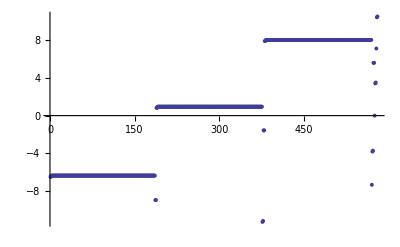

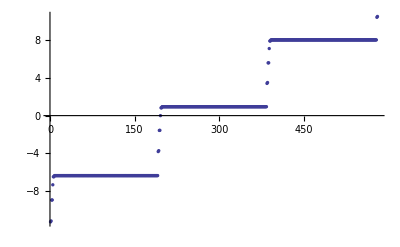

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);


EMatrixelement[{60,0,1/2,1/2},{63,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{62,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{61,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{60,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{59,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{57,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{56,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

{98|1|1/2|1/2,98|1|3/2|1/2,97|2|3/2|1/2,97|2|5/2|1/2,99|0|1/2|1/2,96|3|7/2|1/2,96|3|5/2|1/2,96|4|7/2|1/2,96|4|9/2|1/2,96|5|9/2|1/2,96|5|11/2|1/2,96|6|11/2|1/2,96|6|13/2|1/2,96|7|13/2|1/2,96|7|15/2|1/2,96|8|15/2|1/2,96|8|17/2|1/2,96|9|17/2|1/2,96|9|19/2|1/2,96|10|19/2|1/2,96|10|21/2|1/2,96|11|21/2|1/2,96|11|23/2|1/2,96|12|23/2|1/2,96|12|25/2|1/2,96|13|25/2|1/2,96|13|27/2|1/2,96|14|27/2|1/2,96|14|29/2|1/2,96|15|29/2|1/2,96|15|31/2|1/2,96|16|31/2|1/2,96|16|33/2|1/2,96|17|33/2|1/2,96|17|35/2|1/2,96|18|35/2|1/2,96|18|37/2|1/2,96|19|37/2|1/2,96|19|39/2|1/2,96|20|39/2|1/2,96|20|41/2|1/2,96|21|41/2|1/2,96|21|43/2|1/2,96|22|43/2|1/2,96|22|45/2|1/2,96|23|45/2|1/2,96|23|47/2|1/2,96|24|47/2|1/2,96|24|49/2|1/2,96|25|49/2|1/2,96|25|51/2|1/2,96|26|51/2|1/2,96|26|53/2|1/2,96|27|53/2|1/2,96|27|55/2|1/2,96|28|55/2|1/2,96|28|57/2|1/2,96|29|57/2|1/2,96|29|59/2|1/2,96|30|59/2|1/2,96|30|61/2|1/2,96|31|61/2|1/2,96|31|63/2|1/2,96|32|63/2|1/2,96|32|65/2|1/2,96|33|65/2|1/2,96|33|67/2|1/2,96|34|67/2|1/2,96|34|69/2|1/2,96|35|69/2|1/2,96|35|71/2|1/2,96|36|71/2|1/2,96|36|73/2|1/2,96|37|73/2|1/2,96|37|75/2|1/2,96|38|75/2|1/2,96|38|77/2|1/2,96|39|77/2|1/2,96|39|79/2|1/2,96|40|79/2|1/2,96|40|81/2|1/2,96|41|81/2|1/2,96|41|83/2|1/2,96|42|83/2|1/2,96|42|85/2|1/2,96|43|85/2|1/2,96|43|87/2|1/2,96|44|87/2|1/2,96|44|89/2|1/2,96|45|89/2|1/2,96|45|91/2|1/2,96|46|91/2|1/2,96|46|93/2|1/2,96|47|93/2|1/2,96|47|95/2|1/2,96|48|95/2|1/2,96|48|97/2|1/2,96|49|97/2|1/2,96|49|99/2|1/2,96|50|99/2|1/2,96|50|101/2|1/2,96|51|101/2|1/2,96|51|103/2|1/2,96|52|103/2|1/2,96|52|105/2|1/2,96|53|105/2|1/2,96|53|107/2|1/2,96|54|107/2|1/2,96|54|109/2|1/2,96|55|109/2|1/2,96|55|111/2|1/2,96|56|111/2|1/2,96|56|113/2|1/2,96|57|113/2|1/2,96|57|115/2|1/2,96|58|115/2|1/2,96|58|117/2|1/2,96|59|117/2|1/2,96|59|119/2|1/2,96|60|119/2|1/2,96|60|121/2|1/2,96|61|121/2|1/2,96|61|123/2|1/2,96|62|123/2|1/2,96|62|125/2|1/2,96|63|125/2|1/2,96|63|127/2|1/2,96|64|127/2|1/2,96|64|129/2|1/2,96|65|129/2|1/2,96|65|131/2|1/2,96|66|131/2|1/2,96|66|133/2|1/2,96|67|133/2|1/2,96|67|135/2|1/2,96|68|135/2|1/2,96|68|137/2|1/2,96|69|137/2|1/2,96|69|139/2|1/2,96|70|139/2|1/2,96|70|141/2|1/2,96|71|141/2|1/2,96|71|143/2|1/2,96|72|143/2|1/2,96|72|145/2|1/2,96|73|145/2|1/2,96|73|147/2|1/2,96|74|147/2|1/2,96|74|149/2|1/2,96|75|149/2|1/2,96|75|151/2|1/2,96|76|151/2|1/2,96|76|153/2|1/2,96|77|153/2|1/2,96|77|155/2|1/2,96|78|155/2|1/2,96|78|157/2|1/2,96|79|157/2|1/2,96|79|159/2|1/2,96|80|159/2|1/2,96|80|161/2|1/2,96|81|161/2|1/2,96|81|163/2|1/2,96|82|163/2|1/2,96|82|165/2|1/2,96|83|165/2|1/2,96|83|167/2|1/2,96|84|167/2|1/2,96|84|169/2|1/2,96|85|169/2|1/2,96|85|171/2|1/2,96|86|171/2|1/2,96|86|173/2|1/2,96|87|173/2|1/2,96|87|175/2|1/2,96|88|175/2|1/2,96|88|177/2|1/2,96|89|177/2|1/2,96|89|179/2|1/2,96|90|179/2|1/2,96|90|181/2|1/2,96|91|181/2|1/2,96|91|183/2|1/2,96|92|183/2|1/2,96|92|185/2|1/2,96|93|185/2|1/2,96|93|187/2|1/2,96|94|187/2|1/2,96|94|189/2|1/2,96|95|189/2|1/2,96|95|191/2|1/2,99|1|1/2|1/2,99|1|3/2|1/2,98|2|3/2|1/2,98|2|5/2|1/2,100|0|1/2|1/2,97|3|7/2|1/2,97|3|5/2|1/2,97|4|7/2|1/2,97|4|9/2|1/2,97|5|9/2|1/2,97|5|11/2|1/2,97|6|11/2|1/2,97|6|13/2|1/2,97|7|13/2|1/2,97|7|15/2|1/2,97|8|15/2|1/2,97|8|17/2|1/2,97|9|17/2|1/2,97|9|19/2|1/2,97|10|19/2|1/2,97|10|21/2|1/2,97|11|21/2|1/2,97|11|23/2|1/2,97|12|23/2|1/2,97|12|25/2|1/2,97|13|25/2|1/2,97|13|27/2|1/2,97|14|27/2|1/2,97|14|29/2|1/2,97|15|29/2|1/2,97|15|31/2|1/2,97|16|31/2|1/2,97|16|33/2|1/2,97|17|33/2|1/2,97|17|35/2|1/2,97|18|35/2|1/2,97|18|37/2|1/2,97|19|37/2|1/2,97|19|39/2|1/2,97|20|39/2|1/2,97|20|41/2|1/2,97|21|41/2|1/2,97|21|43/2|1/2,97|22|43/2|1/2,97|22|45/2|1/2,97|23|45/2|1/2,97|23|47/2|1/2,97|24|47/2|1/2,97|24|49/2|1/2,97|25|49/2|1/2,97|25|51/2|1/2,97|26|51/2|1/2,97|26|53/2|1/2,97|27|53/2|1/2,97|27|55/2|1/2,97|28|55/2|1/2,97|28|57/2|1/2,97|29|57/2|1/2,97|29|59/2|1/2,97|30|59/2|1/2,97|30|61/2|1/2,97|31|61/2|1/2,97|31|63/2|1/2,97|32|63/2|1/2,97|32|65/2|1/2,97|33|65/2|1/2,97|33|67/2|1/2,97|34|67/2|1/2,97|34|69/2|1/2,97|35|69/2|1/2,97|35|71/2|1/2,97|36|71/2|1/2,97|36|73/2|1/2,97|37|73/2|1/2,97|37|75/2|1/2,97|38|75/2|1/2,97|38|77/2|1/2,97|39|77/2|1/2,97|39|79/2|1/2,97|40|79/2|1/2,97|40|81/2|1/2,97|41|81/2|1/2,97|41|83/2|1/2,97|42|83/2|1/2,97|42|85/2|1/2,97|43|85/2|1/2,97|43|87/2|1/2,97|44|87/2|1/2,97|44|89/2|1/2,97|45|89/2|1/2,97|45|91/2|1/2,97|46|91/2|1/2,97|46|93/2|1/2,97|47|93/2|1/2,97|47|95/2|1/2,97|48|95/2|1/2,97|48|97/2|1/2,97|49|97/2|1/2,97|49|99/2|1/2,97|50|99/2|1/2,97|50|101/2|1/2,97|51|101/2|1/2,97|51|103/2|1/2,97|52|103/2|1/2,97|52|105/2|1/2,97|53|105/2|1/2,97|53|107/2|1/2,97|54|107/2|1/2,97|54|109/2|1/2,97|55|109/2|1/2,97|55|111/2|1/2,97|56|111/2|1/2,97|56|113/2|1/2,97|57|113/2|1/2,97|57|115/2|1/2,97|58|115/2|1/2,97|58|117/2|1/2,97|59|117/2|1/2,97|59|119/2|1/2,97|60|119/2|1/2,97|60|121/2|1/2,97|61|121/2|1/2,97|61|123/2|1/2,97|62|123/2|1/2,97|62|125/2|1/2,97|63|125/2|1/2,97|63|127/2|1/2,97|64|127/2|1/2,97|64|129/2|1/2,97|65|129/2|1/2,97|65|131/2|1/2,97|66|131/2|1/2,97|66|133/2|1/2,97|67|133/2|1/2,97|67|135/2|1/2,97|68|135/2|1/2,97|68|137/2|1/2,97|69|137/2|1/2,97|69|139/2|1/2,97|70|139/2|1/2,97|70|141/2|1/2,97|71|141/2|1/2,97|71|143/2|1/2,97|72|143/2|1/2,97|72|145/2|1/2,97|73|145/2|1/2,97|73|147/2|1/2,97|74|147/2|1/2,97|74|149/2|1/2,97|75|149/2|1/2,97|75|151/2|1/2,97|76|151/2|1/2,97|76|153/2|1/2,97|77|153/2|1/2,97|77|155/2|1/2,97|78|155/2|1/2,97|78|157/2|1/2,97|79|157/2|1/2,97|79|159/2|1/2,97|80|159/2|1/2,97|80|161/2|1/2,97|81|161/2|1/2,97|81|163/2|1/2,97|82|163/2|1/2,97|82|165/2|1/2,97|83|165/2|1/2,97|83|167/2|1/2,97|84|167/2|1/2,97|84|169/2|1/2,97|85|169/2|1/2,97|85|171/2|1/2,97|86|171/2|1/2,97|86|173/2|1/2,97|87|173/2|1/2,97|87|175/2|1/2,97|88|175/2|1/2,97|88|177/2|1/2,97|89|177/2|1/2,97|89|179/2|1/2,97|90|179/2|1/2,97|90|181/2|1/2,97|91|181/2|1/2,97|91|183/2|1/2,97|92|183/2|1/2,97|92|185/2|1/2,97|93|185/2|1/2,97|93|187/2|1/2,97|94|187/2|1/2,97|94|189/2|1/2,97|95|189/2|1/2,97|95|191/2|1/2,97|96|191/2|1/2,97|96|193/2|1/2,100|1|1/2|1/2,100|1|3/2|1/2,99|2|3/2|1/2,99|2|5/2|1/2,101|0|1/2|1/2,98|3|7/2|1/2,98|3|5/2|1/2,98|4|7/2|1/2,98|4|9/2|1/2,98|5|9/2|1/2,98|5|11/2|1/2,98|6|11/2|1/2,98|6|13/2|1/2,98|7|13/2|1/2,98|7|15/2|1/2,98|8|15/2|1/2,98|8|17/2|1/2,98|9|17/2|1/2,98|9|19/2|1/2,98|10|19/2|1/2,98|10|21/2|1/2,98|11|21/2|1/2,98|11|23/2|1/2,98|12|23/2|1/2,98|12|25/2|1/2,98|13|25/2|1/2,98|13|27/2|1/2,98|14|27/2|1/2,98|14|29/2|1/2,98|15|29/2|1/2,98|15|31/2|1/2,98|16|31/2|1/2,98|16|33/2|1/2,98|17|33/2|1/2,98|17|35/2|1/2,98|18|35/2|1/2,98|18|37/2|1/2,98|19|37/2|1/2,98|19|39/2|1/2,98|20|39/2|1/2,98|20|41/2|1/2,98|21|41/2|1/2,98|21|43/2|1/2,98|22|43/2|1/2,98|22|45/2|1/2,98|23|45/2|1/2,98|23|47/2|1/2,98|24|47/2|1/2,98|24|49/2|1/2,98|25|49/2|1/2,98|25|51/2|1/2,98|26|51/2|1/2,98|26|53/2|1/2,98|27|53/2|1/2,98|27|55/2|1/2,98|28|55/2|1/2,98|28|57/2|1/2,98|29|57/2|1/2,98|29|59/2|1/2,98|30|59/2|1/2,98|30|61/2|1/2,98|31|61/2|1/2,98|31|63/2|1/2,98|32|63/2|1/2,98|32|65/2|1/2,98|33|65/2|1/2,98|33|67/2|1/2,98|34|67/2|1/2,98|34|69/2|1/2,98|35|69/2|1/2,98|35|71/2|1/2,98|36|71/2|1/2,98|36|73/2|1/2,98|37|73/2|1/2,98|37|75/2|1/2,98|38|75/2|1/2,98|38|77/2|1/2,98|39|77/2|1/2,98|39|79/2|1/2,98|40|79/2|1/2,98|40|81/2|1/2,98|41|81/2|1/2,98|41|83/2|1/2,98|42|83/2|1/2,98|42|85/2|1/2,98|43|85/2|1/2,98|43|87/2|1/2,98|44|87/2|1/2,98|44|89/2|1/2,98|45|89/2|1/2,98|45|91/2|1/2,98|46|91/2|1/2,98|46|93/2|1/2,98|47|93/2|1/2,98|47|95/2|1/2,98|48|95/2|1/2,98|48|97/2|1/2,98|49|97/2|1/2,98|49|99/2|1/2,98|50|99/2|1/2,98|50|101/2|1/2,98|51|101/2|1/2,98|51|103/2|1/2,98|52|103/2|1/2,98|52|105/2|1/2,98|53|105/2|1/2,98|53|107/2|1/2,98|54|107/2|1/2,98|54|109/2|1/2,98|55|109/2|1/2,98|55|111/2|1/2,98|56|111/2|1/2,98|56|113/2|1/2,98|57|113/2|1/2,98|57|115/2|1/2,98|58|115/2|1/2,98|58|117/2|1/2,98|59|117/2|1/2,98|59|119/2|1/2,98|60|119/2|1/2,98|60|121/2|1/2,98|61|121/2|1/2,98|61|123/2|1/2,98|62|123/2|1/2,98|62|125/2|1/2,98|63|125/2|1/2,98|63|127/2|1/2,98|64|127/2|1/2,98|64|129/2|1/2,98|65|129/2|1/2,98|65|131/2|1/2,98|66|131/2|1/2,98|66|133/2|1/2,98|67|133/2|1/2,98|67|135/2|1/2,98|68|135/2|1/2,98|68|137/2|1/2,98|69|137/2|1/2,98|69|139/2|1/2,98|70|139/2|1/2,98|70|141/2|1/2,98|71|141/2|1/2,98|71|143/2|1/2,98|72|143/2|1/2,98|72|145/2|1/2,98|73|145/2|1/2,98|73|147/2|1/2,98|74|147/2|1/2,98|74|149/2|1/2,98|75|149/2|1/2,98|75|151/2|1/2,98|76|151/2|1/2,98|76|153/2|1/2,98|77|153/2|1/2,98|77|155/2|1/2,98|78|155/2|1/2,98|78|157/2|1/2,98|79|157/2|1/2,98|79|159/2|1/2,98|80|159/2|1/2,98|80|161/2|1/2,98|81|161/2|1/2,98|81|163/2|1/2,98|82|163/2|1/2,98|82|165/2|1/2,98|83|165/2|1/2,98|83|167/2|1/2,98|84|167/2|1/2,98|84|169/2|1/2,98|85|169/2|1/2,98|85|171/2|1/2,98|86|171/2|1/2,98|86|173/2|1/2,98|87|173/2|1/2,98|87|175/2|1/2,98|88|175/2|1/2,98|88|177/2|1/2,98|89|177/2|1/2,98|89|179/2|1/2,98|90|179/2|1/2,98|90|181/2|1/2,98|91|181/2|1/2,98|91|183/2|1/2,98|92|183/2|1/2,98|92|185/2|1/2,98|93|185/2|1/2,98|93|187/2|1/2,98|94|187/2|1/2,98|94|189/2|1/2,98|95|189/2|1/2,98|95|191/2|1/2,98|96|191/2|1/2,98|96|193/2|1/2,98|97|193/2|1/2,98|97|195/2|1/2,101|1|1/2|1/2,101|1|3/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{33.1198,0.-33.1198 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-59.3791,0.+59.3791 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{148.558,0.-148.558 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-1247.21,0.+1247.21 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-1134.82,0.+1134.82 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.499,0.-160.499 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-65.4644,0.+65.4644 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{36.246,0.-36.246 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{29.999,Null}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-3.57091×10^11,-3.57091×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.56968×10^11,-3.59571×10^11,-3.59558×10^11,-3.49765×10^11,-3.49765×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.49646×10^11,-3.61889×10^11,-3.61789×10^11,-3.52169×10^11,-3.52157×10^11,-3.42662×10^11,-3.42663×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.42547×10^11,-3.57946×10^11,-3.54416×10^11,-3.54319×10^11,-3.44993×10^11,-3.44981×10^11,-3.50594×10^11,-3.47171×10^11,-3.47077×10^11,-3.43466×10^11,-3.40147×10^11,-3.40056×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-361.892,-361.793,-359.571,-359.558,-357.946,-357.155,-357.152,-357.141,-357.141,-357.137,-357.137,-357.133,-357.133,-357.129,-357.129,-357.125,-357.125,-357.121,-357.121,-357.117,-357.117,-357.114,-357.113,-357.11,-357.11,-357.106,-357.106,-357.102,-357.102,-357.098,-357.098,-357.094,-357.094,-357.091,-357.091,-357.087,-357.087,-357.083,-357.083,-357.079,-357.079,-357.075,-357.075,-357.072,-357.072,-357.068,-357.068,-357.064,-357.064,-357.06,-357.06,-357.057,-357.056,-357.053,-357.053,-357.049,-357.049,-357.045,-357.045,-357.041,-357.041,-357.038,-357.038,-357.034,-357.034,-357.03,-357.03,-357.026,-357.026,-357.023,-357.023,-357.019,-357.019,-357.015,-357.015,-357.011,-357.011,-357.007,-357.007,-357.004,-357.004,-357.,-357.,-356.996,-356.996,-356.992,-356.992,-356.989,-356.989,-356.985,-356.985,-356.981,-356.981,-356.977,-356.977,-356.974,-356.974,-356.97,-356.97,-356.966,-356.966,-356.962,-356.962,-356.959,-356.959,-356.955,-356.955,-356.951,-356.951,-356.947,-356.947,-356.943,-356.943,-356.94,-356.94,-356.936,-356.936,-356.932,-356.932,-356.928,-356.928,-356.925,-356.925,-356.921,-356.921,-356.917,-356.917,-356.913,-356.913,-356.91,-356.91,-356.906,-356.906,-356.902,-356.902,-356.898,-356.898,-356.895,-356.894,-356.891,-356.891,-356.887,-356.887,-356.883,-356.883,-356.879,-356.879,-356.876,-356.876,-356.872,-356.872,-356.868,-356.868,-356.864,-356.864,-356.861,-356.86,-356.857,-356.857,-356.853,-356.853,-356.849,-356.849,-356.845,-356.845,-356.842,-356.841,-356.838,-356.838,-356.834,-356.834,-356.83,-356.83,-356.826,-356.826,-356.823,-356.822,-356.819,-356.819,-356.815,-356.815,-356.811,-356.811,-356.807,-356.807,-356.804,-356.803,-356.8,-356.799,-356.796,-356.795,-354.418,-354.321,-352.169,-352.156,-350.594,-349.833,-349.83,-349.822,-349.822,-349.818,-349.818,-349.814,-349.814,-349.81,-349.81,-349.806,-349.806,-349.802,-349.802,-349.798,-349.798,-349.794,-349.794,-349.791,-349.79,-349.787,-349.787,-349.783,-349.783,-349.779,-349.779,-349.775,-349.775,-349.771,-349.771,-349.767,-349.767,-349.764,-349.764,-349.76,-349.76,-349.756,-349.756,-349.752,-349.752,-349.748,-349.748,-349.744,-349.744,-349.741,-349.741,-349.737,-349.737,-349.733,-349.733,-349.729,-349.729,-349.725,-349.725,-349.722,-349.722,-349.718,-349.718,-349.714,-349.714,-349.71,-349.71,-349.706,-349.706,-349.703,-349.702,-349.699,-349.699,-349.695,-349.695,-349.691,-349.691,-349.687,-349.687,-349.683,-349.683,-349.68,-349.68,-349.676,-349.676,-349.672,-349.672,-349.668,-349.668,-349.664,-349.664,-349.661,-349.661,-349.657,-349.657,-349.653,-349.653,-349.649,-349.649,-349.645,-349.645,-349.642,-349.642,-349.638,-349.638,-349.634,-349.634,-349.63,-349.63,-349.626,-349.626,-349.623,-349.623,-349.619,-349.619,-349.615,-349.615,-349.611,-349.611,-349.607,-349.607,-349.604,-349.604,-349.6,-349.6,-349.596,-349.596,-349.592,-349.592,-349.588,-349.588,-349.585,-349.585,-349.581,-349.581,-349.577,-349.577,-349.573,-349.573,-349.569,-349.569,-349.566,-349.565,-349.562,-349.562,-349.558,-349.558,-349.554,-349.554,-349.55,-349.55,-349.547,-349.546,-349.543,-349.543,-349.539,-349.539,-349.535,-349.535,-349.531,-349.531,-349.527,-349.527,-349.524,-349.523,-349.52,-349.52,-349.516,-349.516,-349.512,-349.512,-349.508,-349.508,-349.505,-349.504,-349.501,-349.5,-349.497,-349.497,-349.493,-349.493,-349.489,-349.489,-349.485,-349.485,-349.481,-349.481,-349.478,-349.477,-349.474,-349.473,-349.47,-349.469,-347.174,-347.08,-344.993,-344.981,-343.466,-342.735,-342.732,-342.726,-342.726,-342.722,-342.722,-342.718,-342.718,-342.714,-342.714,-342.71,-342.71,-342.706,-342.706,-342.702,-342.702,-342.698,-342.698,-342.694,-342.694,-342.69,-342.69,-342.687,-342.686,-342.683,-342.683,-342.679,-342.679,-342.675,-342.675,-342.671,-342.671,-342.667,-342.667,-342.663,-342.663,-342.659,-342.659,-342.656,-342.655,-342.652,-342.652,-342.648,-342.648,-342.644,-342.644,-342.64,-342.64,-342.636,-342.636,-342.632,-342.632,-342.629,-342.629,-342.625,-342.625,-342.621,-342.621,-342.617,-342.617,-342.613,-342.613,-342.609,-342.609,-342.605,-342.605,-342.602,-342.602,-342.598,-342.598,-342.594,-342.594,-342.59,-342.59,-342.586,-342.586,-342.582,-342.582,-342.579,-342.579,-342.575,-342.575,-342.571,-342.571,-342.567,-342.567,-342.563,-342.563,-342.559,-342.559,-342.556,-342.555,-342.552,-342.552,-342.548,-342.548,-342.544,-342.544,-342.54,-342.54,-342.536,-342.536,-342.532,-342.532,-342.529,-342.529,-342.525,-342.525,-342.521,-342.521,-342.517,-342.517,-342.513,-342.513,-342.509,-342.509,-342.506,-342.506,-342.502,-342.502,-342.498,-342.498,-342.494,-342.494,-342.49,-342.49,-342.486,-342.486,-342.483,-342.482,-342.479,-342.479,-342.475,-342.475,-342.471,-342.471,-342.467,-342.467,-342.463,-342.463,-342.459,-342.459,-342.456,-342.456,-342.452,-342.452,-342.448,-342.448,-342.444,-342.444,-342.44,-342.44,-342.436,-342.436,-342.433,-342.432,-342.429,-342.429,-342.425,-342.425,-342.421,-342.421,-342.417,-342.417,-342.413,-342.413,-342.409,-342.409,-342.406,-342.405,-342.402,-342.401,-342.398,-342.398,-342.394,-342.394,-342.39,-342.39,-342.386,-342.386,-342.382,-342.382,-342.378,-342.378,-342.374,-342.374,-342.371,-342.37,-342.367,-342.366,-340.146,-340.054}

{{300,-68.7129,98|1|1/2|1/2},{300,-68.0677,98|1|3/2|1/2},{300,-67.6403,97|2|3/2|1/2},{300,-67.0177,97|2|5/2|1/2},{300,-66.5774,99|0|1/2|1/2},{300,-65.9666,96|3|7/2|1/2},{300,-65.5163,96|3|5/2|1/2},{300,-64.9139,96|4|7/2|1/2},{300,-64.4551,96|4|9/2|1/2},{300,-63.8595,96|5|9/2|1/2},{300,-63.3933,96|5|11/2|1/2},{300,-62.8032,96|6|11/2|1/2},{300,-62.3307,96|6|13/2|1/2},{300,-61.7453,96|7|13/2|1/2},{300,-61.2674,96|7|15/2|1/2},{300,-60.6857,96|8|15/2|1/2},{300,-60.2037,96|8|17/2|1/2},{300,-59.6248,96|9|17/2|1/2},{300,-59.1403,96|9|19/2|1/2},{300,-58.5625,96|10|19/2|1/2},{300,-58.0792,96|10|21/2|1/2},{300,-57.4992,96|11|21/2|1/2},{300,-57.0314,96|11|23/2|1/2},{300,-56.4353,96|12|23/2|1/2},{300,-56.3558,96|12|25/2|1/2},{300,-55.908,96|13|25/2|1/2},{300,-55.7068,96|13|27/2|1/2},{300,-55.3689,96|14|27/2|1/2},{300,-55.2576,96|14|29/2|1/2},{300,-54.8284,96|15|29/2|1/2},{300,-54.6072,96|15|31/2|1/2},{300,-54.3008,96|16|31/2|1/2},{300,-54.1572,96|16|33/2|1/2},{300,-53.7536,96|17|33/2|1/2},{300,-53.5045,96|17|35/2|1/2},{300,-53.2313,96|18|35/2|1/2},{300,-53.0518,96|18|37/2|1/2},{300,-52.6803,96|19|37/2|1/2},{300,-52.3984,96|19|39/2|1/2},{300,-52.1601,96|20|39/2|1/2},{300,-51.9408,96|20|41/2|1/2},{300,-51.6074,96|21|41/2|1/2},{300,-51.289,96|21|43/2|1/2},{300,-51.0869,96|22|43/2|1/2},{300,-50.8244,96|22|45/2|1/2},{300,-50.5343,96|23|45/2|1/2},{300,-50.1771,96|23|47/2|1/2},{300,-50.0111,96|24|47/2|1/2},{300,-49.7028,96|24|49/2|1/2},{300,-49.4603,96|25|49/2|1/2},{300,-49.0645,96|25|51/2|1/2},{300,-48.9308,96|26|51/2|1/2},{300,-48.5767,96|26|53/2|1/2},{300,-48.3847,96|27|53/2|1/2},{300,-47.955,96|27|55/2|1/2},{300,-47.8422,96|28|55/2|1/2},{300,-47.4478,96|28|57/2|1/2},{300,-47.306,96|29|57/2|1/2},{300,-46.8544,96|29|59/2|1/2},{300,-46.7396,96|30|59/2|1/2},{300,-46.3211,96|30|61/2|1/2},{300,-46.2193,96|31|61/2|1/2},{300,-45.7643,96|31|63/2|1/2},{300,-45.6215,96|32|63/2|1/2},{300,-45.2091,96|32|65/2|1/2},{300,-45.1122,96|33|65/2|1/2},{300,-44.6803,96|33|67/2|1/2},{300,-44.4923,96|34|67/2|1/2},{300,-44.1169,96|34|69/2|1/2},{300,-43.9796,96|35|69/2|1/2},{300,-43.5989,96|35|71/2|1/2},{300,-43.3556,96|36|71/2|1/2},{300,-43.0337,96|36|73/2|1/2},{300,-42.8328,96|37|73/2|1/2},{300,-42.5183,96|37|75/2|1/2},{300,-42.2135,96|38|75/2|1/2},{300,-41.953,96|38|77/2|1/2},{300,-41.6785,96|39|77/2|1/2},{300,-41.4375,96|39|79/2|1/2},{300,-41.067,96|40|79/2|1/2},{300,-40.8726,96|40|81/2|1/2},{300,-40.5191,96|41|81/2|1/2},{300,-40.3561,96|41|83/2|1/2},{300,-39.9168,96|42|83/2|1/2},{300,-39.7918,96|42|85/2|1/2},{300,-39.3558,96|43|85/2|1/2},{300,-39.2737,96|43|87/2|1/2},{300,-38.7635,96|44|87/2|1/2},{300,-38.7102,96|44|89/2|1/2},{300,-38.1902,96|45|89/2|1/2},{300,-38.1897,96|45|91/2|1/2},{300,-37.6276,96|46|91/2|1/2},{300,-37.608,96|46|93/2|1/2},{300,-37.1052,96|47|93/2|1/2},{300,-37.0228,96|47|95/2|1/2},{300,-36.5439,96|48|95/2|1/2},{300,-36.4516,96|48|97/2|1/2},{300,-36.0184,96|49|97/2|1/2},{300,-35.8601,96|49|99/2|1/2},{300,-35.459,96|50|99/2|1/2},{300,-35.2965,96|50|101/2|1/2},{300,-34.929,96|51|101/2|1/2},{300,-34.7253,96|51|103/2|1/2},{300,-34.3728,96|52|103/2|1/2},{300,-34.1485,96|52|105/2|1/2},{300,-33.8546,96|53|105/2|1/2},{300,-33.836,96|53|107/2|1/2},{300,-33.306,96|54|107/2|1/2},{300,-33.2813,96|54|109/2|1/2},{300,-33.0489,96|55|109/2|1/2},{300,-32.7443,96|55|111/2|1/2},{300,-32.7248,96|56|111/2|1/2},{300,-32.6426,96|56|113/2|1/2},{300,-32.1949,96|57|113/2|1/2},{300,-32.1749,96|57|115/2|1/2},{300,-31.9348,96|58|115/2|1/2},{300,-31.6503,96|58|117/2|1/2},{300,-31.5816,96|59|117/2|1/2},{300,-31.5237,96|59|119/2|1/2},{300,-31.1053,96|60|119/2|1/2},{300,-31.0117,96|60|121/2|1/2},{300,-30.8257,96|61|121/2|1/2},{300,-30.5572,96|61|123/2|1/2},{300,-30.4294,96|62|123/2|1/2},{300,-30.4199,96|62|125/2|1/2},{300,-30.0139,96|63|125/2|1/2},{300,-29.8319,96|63|127/2|1/2},{300,-29.7238,96|64|127/2|1/2},{300,-29.4641,96|64|129/2|1/2},{300,-29.3219,96|65|129/2|1/2},{300,-29.27,96|65|131/2|1/2},{300,-28.9209,96|66|131/2|1/2},{300,-28.6432,96|66|133/2|1/2},{300,-28.6277,96|67|133/2|1/2},{300,-28.3705,96|67|135/2|1/2},{300,-28.2269,96|68|135/2|1/2},{300,-28.1067,96|68|137/2|1/2},{300,-27.8263,96|69|137/2|1/2},{300,-27.5346,96|69|139/2|1/2},{300,-27.4492,96|70|139/2|1/2},{300,-27.2758,96|70|141/2|1/2},{300,-27.1339,96|71|141/2|1/2},{300,-26.9439,96|71|143/2|1/2},{300,-26.7299,96|72|143/2|1/2},{300,-26.4405,96|72|145/2|1/2},{300,-26.2519,96|73|145/2|1/2},{300,-26.1797,96|73|147/2|1/2},{300,-26.0419,96|74|147/2|1/2},{300,-25.7876,96|74|149/2|1/2},{300,-25.6316,96|75|149/2|1/2},{300,-25.3395,96|75|151/2|1/2},{300,-25.082,96|76|151/2|1/2},{300,-25.0552,96|76|153/2|1/2},{300,-24.9477,96|77|153/2|1/2},{300,-24.645,96|77|155/2|1/2},{300,-24.5317,96|78|155/2|1/2},{300,-24.2241,96|78|157/2|1/2},{300,-23.9824,96|79|157/2|1/2},{300,-23.8915,96|79|159/2|1/2},{300,-23.8194,96|80|159/2|1/2},{300,-23.5219,96|80|161/2|1/2},{300,-23.43,96|81|161/2|1/2},{300,-23.088,96|81|163/2|1/2},{300,-22.8811,96|82|163/2|1/2},{300,-22.7925,96|82|165/2|1/2},{300,-22.6255,96|83|165/2|1/2},{300,-22.4179,96|83|167/2|1/2},{300,-22.3269,96|84|167/2|1/2},{300,-21.9307,96|84|169/2|1/2},{300,-21.7782,96|85|169/2|1/2},{300,-21.7057,96|85|171/2|1/2},{300,-21.4189,96|86|171/2|1/2},{300,-21.3277,96|86|173/2|1/2},{300,-21.2224,96|87|173/2|1/2},{300,-20.7575,96|87|175/2|1/2},{300,-20.6737,96|88|175/2|1/2},{300,-20.6218,96|88|177/2|1/2},{300,-20.2448,96|89|177/2|1/2},{300,-20.2091,96|89|179/2|1/2},{300,-20.1167,96|90|179/2|1/2},{300,-19.579,96|90|181/2|1/2},{300,-19.5638,96|91|181/2|1/2},{300,-19.5397,96|91|183/2|1/2},{300,-19.1638,96|92|183/2|1/2},{300,-19.0139,96|92|185/2|1/2},{300,-18.9934,96|93|185/2|1/2},{300,-18.4633,96|93|187/2|1/2},{300,-18.4591,96|94|187/2|1/2},{300,-18.3876,96|94|189/2|1/2},{300,-18.079,96|95|189/2|1/2},{300,-17.9043,96|95|191/2|1/2},{300,-17.7825,99|1|1/2|1/2},{300,-17.3797,99|1|3/2|1/2},{300,-17.3557,98|2|3/2|1/2},{300,-17.211,98|2|5/2|1/2},{300,-16.9803,100|0|1/2|1/2},{300,-16.7964,97|3|7/2|1/2},{300,-16.5687,97|3|5/2|1/2},{300,-16.3009,97|4|7/2|1/2},{300,-16.2476,97|4|9/2|1/2},{300,-16.0625,97|5|9/2|1/2},{300,-15.8487,97|5|11/2|1/2},{300,-15.688,97|6|11/2|1/2},{300,-15.3572,97|6|13/2|1/2},{300,-15.2205,97|7|13/2|1/2},{300,-15.139,97|7|15/2|1/2},{300,-14.9507,97|8|15/2|1/2},{300,-14.6762,97|8|17/2|1/2},{300,-14.5792,97|9|17/2|1/2},{300,-14.1802,97|9|19/2|1/2},{300,-14.1065,97|10|19/2|1/2},{300,-14.03,97|10|21/2|1/2},{300,-13.8585,97|11|21/2|1/2},{300,-13.4805,97|11|23/2|1/2},{300,-13.4701,97|12|23/2|1/2},{300,-13.0908,97|12|25/2|1/2},{300,-12.9212,97|13|25/2|1/2},{300,-12.9064,97|13|27/2|1/2},{300,-12.7728,97|14|27/2|1/2},{300,-12.3612,97|14|29/2|1/2},{300,-12.275,97|15|29/2|1/2},{300,-12.0178,97|15|31/2|1/2},{300,-11.8131,97|16|31/2|1/2},{300,-11.692,97|16|33/2|1/2},{300,-11.688,97|17|33/2|1/2},{300,-11.2528,97|17|35/2|1/2},{300,-11.0654,97|18|35/2|1/2},{300,-10.9487,97|18|37/2|1/2},{300,-10.7067,97|19|37/2|1/2},{300,-10.6011,97|19|39/2|1/2},{300,-10.4765,97|20|39/2|1/2},{300,-10.1456,97|20|41/2|1/2},{300,-9.88218,97|21|41/2|1/2},{300,-9.85516,97|21|43/2|1/2},{300,-9.6028,97|22|43/2|1/2},{300,-9.50924,97|22|45/2|1/2},{300,-9.26315,97|23|45/2|1/2},{300,-9.04052,97|23|47/2|1/2},{300,-8.8168,97|24|47/2|1/2},{300,-8.65025,97|24|49/2|1/2},{300,-8.49906,97|25|49/2|1/2},{300,-8.41004,97|25|51/2|1/2},{300,-8.05887,97|26|51/2|1/2},{300,-7.93595,97|26|53/2|1/2},{300,-7.74916,97|27|53/2|1/2},{300,-7.47571,97|27|55/2|1/2},{300,-7.37496,97|28|55/2|1/2},{300,-7.29972,97|28|57/2|1/2},{300,-6.90437,97|29|57/2|1/2},{300,-6.80284,97|29|59/2|1/2},{300,-6.66981,97|30|59/2|1/2},{300,-6.36204,97|30|61/2|1/2},{300,-6.22695,97|31|61/2|1/2},{300,-6.15204,97|31|63/2|1/2},{300,-5.82804,97|32|63/2|1/2},{300,-5.64645,97|32|65/2|1/2},{300,-5.54724,97|33|65/2|1/2},{300,-5.27187,97|33|67/2|1/2},{300,-5.10681,97|34|67/2|1/2},{300,-4.95348,97|34|69/2|1/2},{300,-4.78539,97|35|69/2|1/2},{300,-4.53264,97|35|71/2|1/2},{300,-4.3619,97|36|71/2|1/2},{300,-4.18774,97|36|73/2|1/2},{300,-3.99425,97|37|73/2|1/2},{300,-3.75967,97|37|75/2|1/2},{300,-3.74283,97|38|75/2|1/2},{300,-3.42929,97|38|77/2|1/2},{300,-3.16487,97|39|77/2|1/2},{300,-3.10622,97|39|79/2|1/2},{300,-2.88342,97|40|79/2|1/2},{300,-2.73791,97|40|81/2|1/2},{300,-2.53107,97|41|81/2|1/2},{300,-2.32668,97|41|83/2|1/2},{300,-2.02689,97|42|83/2|1/2},{300,-1.98623,97|42|85/2|1/2},{300,-1.77381,97|43|85/2|1/2},{300,-1.6975,97|43|87/2|1/2},{300,-1.3229,97|44|87/2|1/2},{300,-1.2248,97|44|89/2|1/2},{300,-0.947495,97|45|89/2|1/2},{300,-0.86984,97|45|91/2|1/2},{300,-0.665634,97|46|91/2|1/2},{300,-0.59273,97|46|93/2|1/2},{300,-0.127509,97|47|93/2|1/2},{300,-0.124445,97|47|95/2|1/2},{300,0.136391,97|48|95/2|1/2},{300,0.182669,97|48|97/2|1/2},{300,0.440693,97|49|97/2|1/2},{300,0.582067,97|49|99/2|1/2},{300,0.973127,97|50|99/2|1/2},{300,1.02841,97|50|101/2|1/2},{300,1.21149,97|51|101/2|1/2},{300,1.2515,97|51|103/2|1/2},{300,1.54461,97|52|103/2|1/2},{300,1.78408,97|52|105/2|1/2},{300,2.06651,97|53|105/2|1/2},{300,2.11372,97|53|107/2|1/2},{300,2.24646,97|54|107/2|1/2},{300,2.41336,97|54|109/2|1/2},{300,2.64542,97|55|109/2|1/2},{300,2.99446,97|55|111/2|1/2},{300,3.14294,97|56|111/2|1/2},{300,3.15667,97|56|113/2|1/2},{300,3.2899,97|57|113/2|1/2},{300,3.60381,97|57|115/2|1/2},{300,3.74248,97|58|115/2|1/2},{300,4.1504,97|58|117/2|1/2},{300,4.20526,97|59|117/2|1/2},{300,4.23471,97|59|119/2|1/2},{300,4.34935,97|60|119/2|1/2},{300,4.79015,97|60|121/2|1/2},{300,4.83965,97|61|121/2|1/2},{300,5.1601,97|61|123/2|1/2},{300,5.30214,97|62|123/2|1/2},{300,5.40152,97|62|125/2|1/2},{300,5.44514,97|63|125/2|1/2},{300,5.90642,97|63|127/2|1/2},{300,5.97898,97|64|127/2|1/2},{300,6.21455,97|64|129/2|1/2},{300,6.37242,97|65|129/2|1/2},{300,6.49706,97|65|131/2|1/2},{300,6.64796,97|66|131/2|1/2},{300,6.98719,97|66|133/2|1/2},{300,7.1002,97|67|133/2|1/2},{300,7.34608,97|67|135/2|1/2},{300,7.44634,97|68|135/2|1/2},{300,7.58354,97|68|137/2|1/2},{300,7.86423,97|69|137/2|1/2},{300,8.06526,97|69|139/2|1/2},{300,8.19,97|70|139/2|1/2},{300,8.52457,97|70|141/2|1/2},{300,8.53136,97|71|141/2|1/2},{300,8.67009,97|71|143/2|1/2},{300,9.08188,97|72|143/2|1/2},{300,9.14542,97|72|145/2|1/2},{300,9.27101,97|73|145/2|1/2},{300,9.60997,97|73|147/2|1/2},{300,9.73258,97|74|147/2|1/2},{300,9.75631,97|74|149/2|1/2},{300,10.2285,97|75|149/2|1/2},{300,10.3,97|75|151/2|1/2},{300,10.3484,97|76|151/2|1/2},{300,10.6993,97|76|153/2|1/2},{300,10.8418,97|77|153/2|1/2},{300,10.9402,97|77|155/2|1/2},{300,11.3139,97|78|155/2|1/2},{300,11.4226,97|78|157/2|1/2},{300,11.5178,97|79|157/2|1/2},{300,11.7931,97|79|159/2|1/2},{300,11.9266,97|80|159/2|1/2},{300,12.1488,97|80|161/2|1/2},{300,12.4,97|81|161/2|1/2},{300,12.4941,97|81|163/2|1/2},{300,12.7334,97|82|163/2|1/2},{300,12.8923,97|82|165/2|1/2},{300,13.0105,97|83|165/2|1/2},{300,13.3538,97|83|167/2|1/2},{300,13.4859,97|84|167/2|1/2},{300,13.5659,97|84|169/2|1/2},{300,13.9334,97|85|169/2|1/2},{300,14.0094,97|85|171/2|1/2},{300,14.0938,97|86|171/2|1/2},{300,14.5237,97|86|173/2|1/2},{300,14.5925,97|87|173/2|1/2},{300,14.6476,97|87|175/2|1/2},{300,15.0678,97|88|175/2|1/2},{300,15.1738,97|88|177/2|1/2},{300,15.1962,97|89|177/2|1/2},{300,15.6039,97|89|179/2|1/2},{300,15.7145,97|90|179/2|1/2},{300,15.7992,97|90|181/2|1/2},{300,16.1742,97|91|181/2|1/2},{300,16.2571,97|91|183/2|1/2},{300,16.408,97|92|183/2|1/2},{300,16.6626,97|92|185/2|1/2},{300,16.8075,97|93|185/2|1/2},{300,16.9987,97|93|187/2|1/2},{300,17.2774,97|94|187/2|1/2},{300,17.3382,97|94|189/2|1/2},{300,17.6246,97|95|189/2|1/2},{300,17.7189,97|95|191/2|1/2},{300,17.901,97|96|191/2|1/2},{300,18.1989,97|96|193/2|1/2},{300,18.3799,100|1|1/2|1/2},{300,18.4188,100|1|3/2|1/2},{300,18.7797,99|2|3/2|1/2},{300,18.8416,99|2|5/2|1/2},{300,18.9957,101|0|1/2|1/2},{300,19.3937,98|3|7/2|1/2},{300,19.4807,98|3|5/2|1/2},{300,19.5004,98|4|7/2|1/2},{300,19.85,98|4|9/2|1/2},{300,20.0578,98|5|9/2|1/2},{300,20.0913,98|5|11/2|1/2},{300,20.5708,98|6|11/2|1/2},{300,20.5775,98|6|13/2|1/2},{300,20.5919,98|7|13/2|1/2},{300,20.9356,98|7|15/2|1/2},{300,21.1874,98|8|15/2|1/2},{300,21.2729,98|8|17/2|1/2},{300,21.6503,98|9|17/2|1/2},{300,21.6931,98|9|19/2|1/2},{300,21.7419,98|10|19/2|1/2},{300,22.0446,98|10|21/2|1/2},{300,22.2839,98|11|21/2|1/2},{300,22.4865,98|11|23/2|1/2},{300,22.727,98|12|23/2|1/2},{300,22.7958,98|12|25/2|1/2},{300,22.8799,98|13|25/2|1/2},{300,23.1835,98|13|27/2|1/2},{300,23.3806,98|14|27/2|1/2},{300,23.698,98|14|29/2|1/2},{300,23.8017,98|15|29/2|1/2},{300,23.899,98|15|31/2|1/2},{300,23.9952,98|16|31/2|1/2},{300,24.3469,98|16|33/2|1/2},{300,24.4779,98|17|33/2|1/2},{300,24.8738,98|17|35/2|1/2},{300,24.9061,98|18|35/2|1/2},{300,25.0032,98|18|37/2|1/2},{300,25.0984,98|19|37/2|1/2},{300,25.5207,98|19|39/2|1/2},{300,25.5785,98|20|39/2|1/2},{300,25.9421,98|20|41/2|1/2},{300,26.0888,98|21|41/2|1/2},{300,26.1301,98|21|43/2|1/2},{300,26.197,98|22|43/2|1/2},{300,26.659,98|22|45/2|1/2},{300,26.7196,98|23|45/2|1/2},{300,27.0048,98|23|47/2|1/2},{300,27.1991,98|24|47/2|1/2},{300,27.2948,98|24|49/2|1/2},{300,27.326,98|25|49/2|1/2},{300,27.7581,98|25|51/2|1/2},{300,27.9004,98|26|51/2|1/2},{300,28.0588,98|26|53/2|1/2},{300,28.3005,98|27|53/2|1/2},{300,28.3935,98|27|55/2|1/2},{300,28.527,98|28|55/2|1/2},{300,28.853,98|28|57/2|1/2},{300,29.0833,98|29|57/2|1/2},{300,29.0999,98|29|59/2|1/2},{300,29.4003,98|30|59/2|1/2},{300,29.4943,98|30|61/2|1/2},{300,29.7248,98|31|61/2|1/2},{300,29.9464,98|31|63/2|1/2},{300,30.124,98|32|63/2|1/2},{300,30.264,98|32|65/2|1/2},{300,30.4993,98|33|65/2|1/2},{300,30.5983,98|33|67/2|1/2},{300,30.9154,98|34|67/2|1/2},{300,31.0385,98|34|69/2|1/2},{300,31.1341,98|35|69/2|1/2},{300,31.4405,98|35|71/2|1/2},{300,31.5975,98|36|71/2|1/2},{300,31.7065,98|36|73/2|1/2},{300,32.0662,98|37|73/2|1/2},{300,32.1293,98|37|75/2|1/2},{300,32.1744,98|38|75/2|1/2},{300,32.6114,98|38|77/2|1/2},{300,32.6948,98|39|77/2|1/2},{300,32.82,98|39|79/2|1/2},{300,33.1154,98|40|79/2|1/2},{300,33.2183,98|40|81/2|1/2},{300,33.3303,98|41|81/2|1/2},{300,33.7774,98|41|83/2|1/2},{300,33.7909,98|42|83/2|1/2},{300,33.9372,98|42|85/2|1/2},{300,34.1771,98|43|85/2|1/2},{300,34.3048,98|43|87/2|1/2},{300,34.5138,98|44|87/2|1/2},{300,34.8855,98|44|89/2|1/2},{300,35.036,98|45|89/2|1/2},{300,35.385,98|45|91/2|1/2},{300,35.6869,98|46|91/2|1/2},{300,35.9712,98|46|93/2|1/2},{300,36.1982,98|47|93/2|1/2},{300,36.4745,98|47|95/2|1/2},{300,36.8634,98|48|95/2|1/2},{300,37.059,98|48|97/2|1/2},{300,37.3567,98|49|97/2|1/2},{300,37.57,98|49|99/2|1/2},{300,38.0359,98|50|99/2|1/2},{300,38.1469,98|50|101/2|1/2},{300,38.5044,98|51|101/2|1/2},{300,38.6752,98|51|103/2|1/2},{300,39.202,98|52|103/2|1/2},{300,39.2361,98|52|105/2|1/2},{300,39.6341,98|53|105/2|1/2},{300,39.7963,98|53|107/2|1/2},{300,40.3167,98|54|107/2|1/2},{300,40.3706,98|54|109/2|1/2},{300,40.745,98|55|109/2|1/2},{300,40.9334,98|55|111/2|1/2},{300,41.4028,98|56|111/2|1/2},{300,41.5272,98|56|113/2|1/2},{300,41.8439,98|57|113/2|1/2},{300,42.0794,98|57|115/2|1/2},{300,42.4871,98|58|115/2|1/2},{300,42.6787,98|58|117/2|1/2},{300,42.9368,98|59|117/2|1/2},{300,43.2281,98|59|119/2|1/2},{300,43.5701,98|60|119/2|1/2},{300,43.824,98|60|121/2|1/2},{300,44.0266,98|61|121/2|1/2},{300,44.3763,98|61|123/2|1/2},{300,44.6519,98|62|123/2|1/2},{300,44.9626,98|62|125/2|1/2},{300,45.1147,98|63|125/2|1/2},{300,45.5225,98|63|127/2|1/2},{300,45.7326,98|64|127/2|1/2},{300,46.0942,98|64|129/2|1/2},{300,46.2016,98|65|129/2|1/2},{300,46.6661,98|65|131/2|1/2},{300,46.8123,98|66|131/2|1/2},{300,47.2185,98|66|133/2|1/2},{300,47.2877,98|67|133/2|1/2},{300,47.8066,98|67|135/2|1/2},{300,47.8913,98|68|135/2|1/2},{300,48.3357,98|68|137/2|1/2},{300,48.3731,98|69|137/2|1/2},{300,48.9437,98|69|139/2|1/2},{300,48.9697,98|70|139/2|1/2},{300,49.4464,98|70|141/2|1/2},{300,49.4579,98|71|141/2|1/2},{300,50.048,98|71|143/2|1/2},{300,50.0774,98|72|143/2|1/2},{300,50.5422,98|72|145/2|1/2},{300,50.5513,98|73|145/2|1/2},{300,51.1267,98|73|147/2|1/2},{300,51.2075,98|74|147/2|1/2},{300,51.6259,98|74|149/2|1/2},{300,51.652,98|75|149/2|1/2},{300,52.2061,98|75|151/2|1/2},{300,52.3341,98|76|151/2|1/2},{300,52.7091,98|76|153/2|1/2},{300,52.7502,98|77|153/2|1/2},{300,53.2865,98|77|155/2|1/2},{300,53.4572,98|78|155/2|1/2},{300,53.7916,98|78|157/2|1/2},{300,53.8478,98|79|157/2|1/2},{300,54.3679,98|79|159/2|1/2},{300,54.5772,98|80|159/2|1/2},{300,54.8732,98|80|161/2|1/2},{300,54.9472,98|81|161/2|1/2},{300,55.4504,98|81|163/2|1/2},{300,55.6944,98|82|163/2|1/2},{300,55.9539,98|82|165/2|1/2},{300,56.0515,98|83|165/2|1/2},{300,56.534,98|83|167/2|1/2},{300,56.8098,98|84|167/2|1/2},{300,57.033,98|84|169/2|1/2},{300,57.169,98|85|169/2|1/2},{300,57.6198,98|85|171/2|1/2},{300,58.1095,98|86|171/2|1/2},{300,58.67,98|86|173/2|1/2},{300,59.19,98|87|173/2|1/2},{300,59.733,98|87|175/2|1/2},{300,60.2711,98|88|175/2|1/2},{300,60.7971,98|88|177/2|1/2},{300,61.3524,98|89|177/2|1/2},{300,61.861,98|89|179/2|1/2},{300,62.4335,98|90|179/2|1/2},{300,62.9244,98|90|181/2|1/2},{300,63.5144,98|91|181/2|1/2},{300,63.9874,98|91|183/2|1/2},{300,64.5949,98|92|183/2|1/2},{300,65.0501,98|92|185/2|1/2},{300,65.6749,98|93|185/2|1/2},{300,66.1129,98|93|187/2|1/2},{300,66.7543,98|94|187/2|1/2},{300,67.1762,98|94|189/2|1/2},{300,67.833,98|95|189/2|1/2},{300,68.2407,98|95|191/2|1/2},{300,68.9113,98|96|191/2|1/2},{300,69.3074,98|96|193/2|1/2},{300,69.9892,98|97|193/2|1/2},{300,70.3784,98|97|195/2|1/2},{300,71.0675,101|1|1/2|1/2},{300,71.4598,101|1|3/2|1/2}}

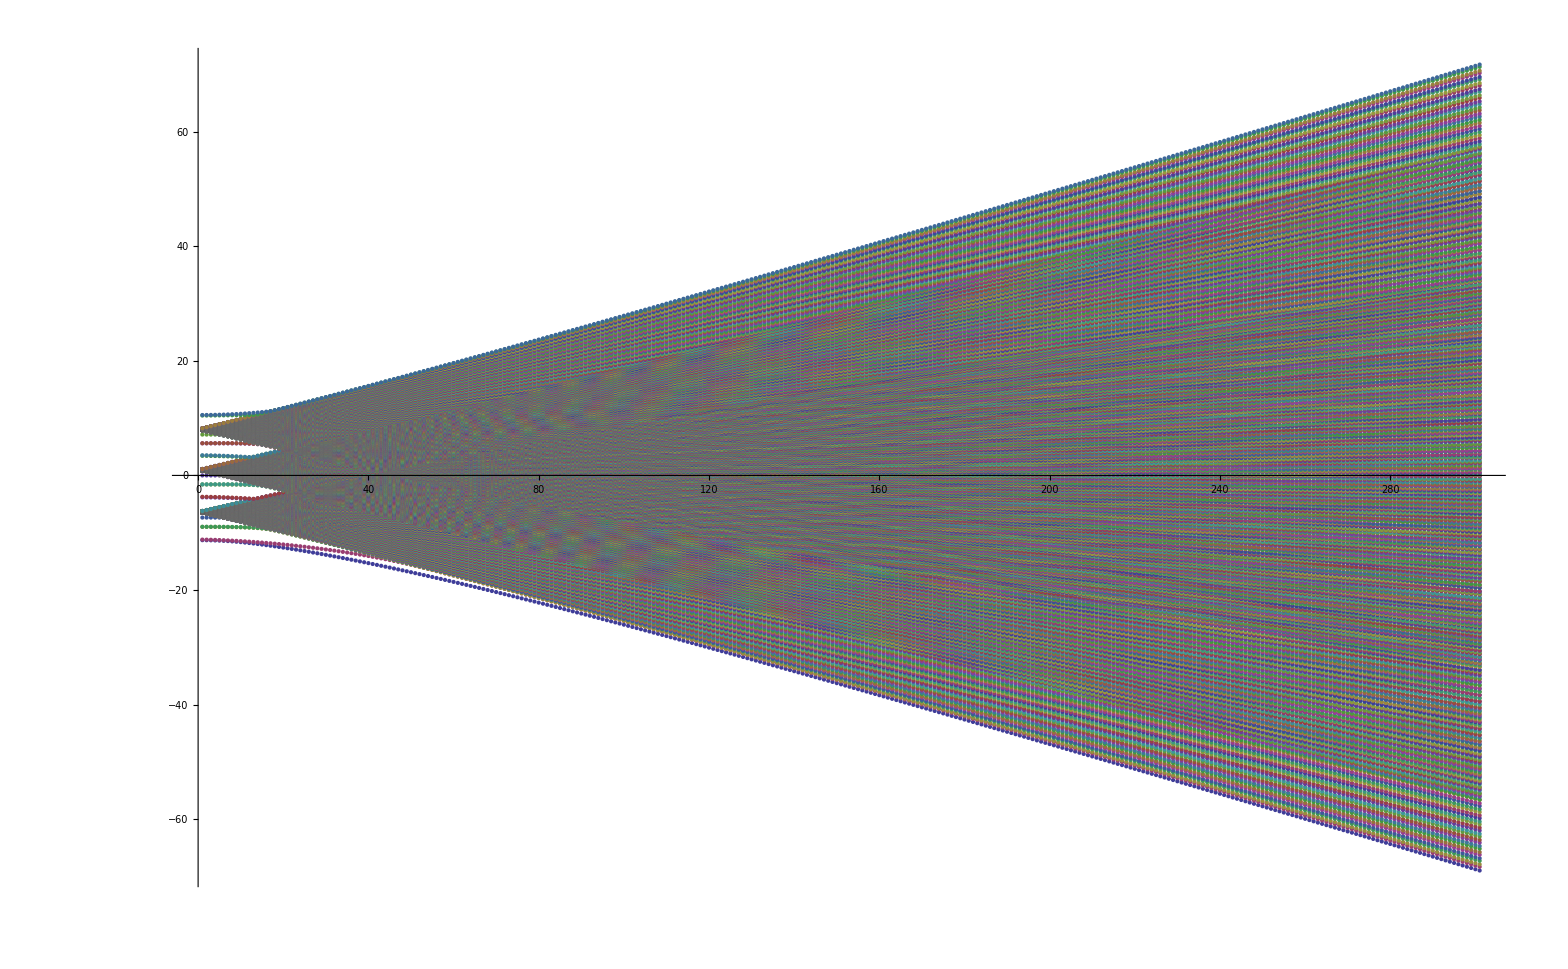

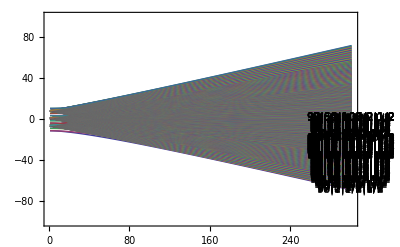

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

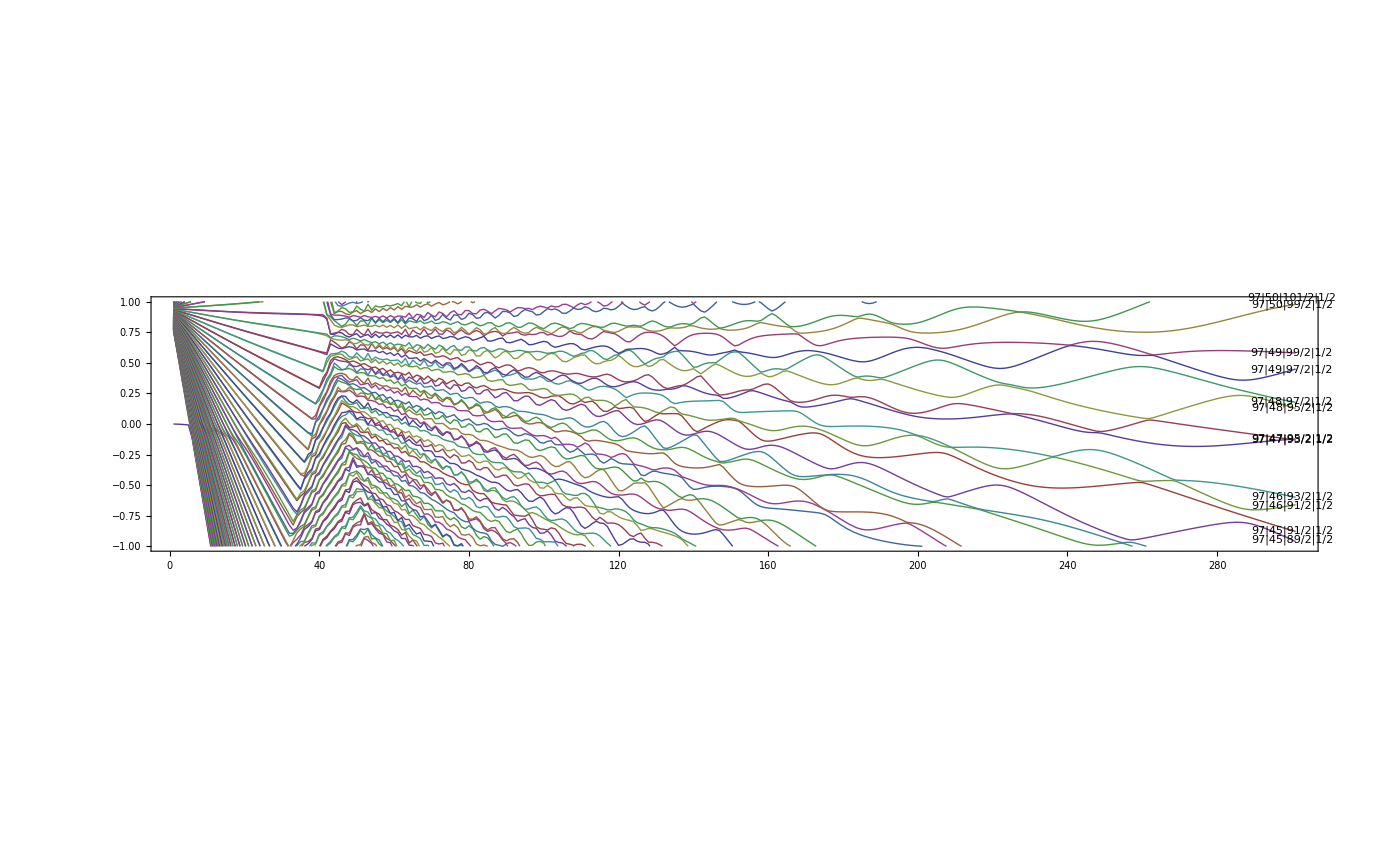

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

{{30,-13.8537,98|1|1/2|1/2},{30,-12.9149,98|1|3/2|1/2},{30,-11.7687,97|2|3/2|1/2},{30,-11.7424,97|2|5/2|1/2},{30,-11.6523,99|0|1/2|1/2},{30,-11.629,96|3|7/2|1/2},{30,-11.5384,96|3|5/2|1/2},{30,-11.5165,96|4|7/2|1/2},{30,-11.4256,96|4|9/2|1/2},{30,-11.4046,96|5|9/2|1/2},{30,-11.3136,96|5|11/2|1/2},{30,-11.2932,96|6|11/2|1/2},{30,-11.202,96|6|13/2|1/2},{30,-11.182,96|7|13/2|1/2},{30,-11.0907,96|7|15/2|1/2},{30,-11.0711,96|8|15/2|1/2},{30,-10.9796,96|8|17/2|1/2},{30,-10.9604,96|9|17/2|1/2},{30,-10.8688,96|9|19/2|1/2},{30,-10.8498,96|10|19/2|1/2},{30,-10.7581,96|10|21/2|1/2},{30,-10.7394,96|11|21/2|1/2},{30,-10.6476,96|11|23/2|1/2},{30,-10.6292,96|12|23/2|1/2},{30,-10.5371,96|12|25/2|1/2},{30,-10.519,96|13|25/2|1/2},{30,-10.4267,96|13|27/2|1/2},{30,-10.4091,96|14|27/2|1/2},{30,-10.3165,96|14|29/2|1/2},{30,-10.2992,96|15|29/2|1/2},{30,-10.2063,96|15|31/2|1/2},{30,-10.1894,96|16|31/2|1/2},{30,-10.0961,96|16|33/2|1/2},{30,-10.0798,96|17|33/2|1/2},{30,-9.98602,96|17|35/2|1/2},{30,-9.97019,96|18|35/2|1/2},{30,-9.87596,96|18|37/2|1/2},{30,-9.86071,96|19|37/2|1/2},{30,-9.76593,96|19|39/2|1/2},{30,-9.7513,96|20|39/2|1/2},{30,-9.65592,96|20|41/2|1/2},{30,-9.64195,96|21|41/2|1/2},{30,-9.54593,96|21|43/2|1/2},{30,-9.53264,96|22|43/2|1/2},{30,-9.43595,96|22|45/2|1/2},{30,-9.42336,96|23|45/2|1/2},{30,-9.32597,96|23|47/2|1/2},{30,-9.3141,96|24|47/2|1/2},{30,-9.21599,96|24|49/2|1/2},{30,-9.20483,96|25|49/2|1/2},{30,-9.106,96|25|51/2|1/2},{30,-9.09554,96|26|51/2|1/2},{30,-8.99602,96|26|53/2|1/2},{30,-8.98621,96|27|53/2|1/2},{30,-8.88605,96|27|55/2|1/2},{30,-8.87684,96|28|55/2|1/2},{30,-8.77609,96|28|57/2|1/2},{30,-8.76742,96|29|57/2|1/2},{30,-8.66618,96|29|59/2|1/2},{30,-8.65793,96|30|59/2|1/2},{30,-8.55639,96|30|61/2|1/2},{30,-8.54837,96|31|61/2|1/2},{30,-8.44689,96|31|63/2|1/2},{30,-8.43875,96|32|63/2|1/2},{30,-8.33824,96|32|65/2|1/2},{30,-8.32906,96|33|65/2|1/2},{30,-8.23351,96|33|67/2|1/2},{30,-8.21932,96|34|67/2|1/2},{30,-8.15793,96|34|69/2|1/2},{30,-8.10955,96|35|69/2|1/2},{30,-8.09692,96|35|71/2|1/2},{30,-7.99976,96|36|71/2|1/2},{30,-7.99606,96|36|73/2|1/2},{30,-7.88988,96|37|73/2|1/2},{30,-7.88769,96|37|75/2|1/2},{30,-7.7798,96|38|75/2|1/2},{30,-7.77802,96|38|77/2|1/2},{30,-7.66953,96|39|77/2|1/2},{30,-7.66796,96|39|79/2|1/2},{30,-7.55912,96|40|79/2|1/2},{30,-7.55771,96|40|81/2|1/2},{30,-7.44861,96|41|81/2|1/2},{30,-7.44731,96|41|83/2|1/2},{30,-7.338,96|42|83/2|1/2},{30,-7.33679,96|42|85/2|1/2},{30,-7.22732,96|43|85/2|1/2},{30,-7.22615,96|43|87/2|1/2},{30,-7.11657,96|44|87/2|1/2},{30,-7.11539,96|44|89/2|1/2},{30,-7.00574,96|45|89/2|1/2},{30,-7.00453,96|45|91/2|1/2},{30,-6.89485,96|46|91/2|1/2},{30,-6.89356,96|46|93/2|1/2},{30,-6.78389,96|47|93/2|1/2},{30,-6.7825,96|47|95/2|1/2},{30,-6.67287,96|48|95/2|1/2},{30,-6.67136,96|48|97/2|1/2},{30,-6.5618,96|49|97/2|1/2},{30,-6.56015,96|49|99/2|1/2},{30,-6.45069,96|50|99/2|1/2},{30,-6.44889,96|50|101/2|1/2},{30,-6.33955,96|51|101/2|1/2},{30,-6.33758,96|51|103/2|1/2},{30,-6.22839,96|52|103/2|1/2},{30,-6.22623,96|52|105/2|1/2},{30,-6.1172,96|53|105/2|1/2},{30,-6.11485,96|53|107/2|1/2},{30,-6.00602,96|54|107/2|1/2},{30,-6.00343,96|54|109/2|1/2},{30,-5.89484,96|55|109/2|1/2},{30,-5.89197,96|55|111/2|1/2},{30,-5.78371,96|56|111/2|1/2},{30,-5.78048,96|56|113/2|1/2},{30,-5.67271,96|57|113/2|1/2},{30,-5.66895,96|57|115/2|1/2},{30,-5.56204,96|58|115/2|1/2},{30,-5.55742,96|58|117/2|1/2},{30,-5.45244,96|59|117/2|1/2},{30,-5.44588,96|59|119/2|1/2},{30,-5.34836,96|60|119/2|1/2},{30,-5.33442,96|60|121/2|1/2},{30,-5.28073,96|61|121/2|1/2},{30,-5.22319,96|61|123/2|1/2},{30,-5.2115,96|62|123/2|1/2},{30,-5.11285,96|62|125/2|1/2},{30,-5.10689,96|63|125/2|1/2},{30,-5.01021,96|63|127/2|1/2},{30,-4.997,96|64|127/2|1/2},{30,-4.96351,96|64|129/2|1/2},{30,-4.88599,96|65|129/2|1/2},{30,-4.88002,96|65|131/2|1/2},{30,-4.77454,96|66|131/2|1/2},{30,-4.77073,96|66|133/2|1/2},{30,-4.66284,96|67|133/2|1/2},{30,-4.65944,96|67|135/2|1/2},{30,-4.55099,96|68|135/2|1/2},{30,-4.54765,96|68|137/2|1/2},{30,-4.43904,96|69|137/2|1/2},{30,-4.43564,96|69|139/2|1/2},{30,-4.39635,96|70|139/2|1/2},{30,-4.37951,96|70|141/2|1/2},{30,-4.327,96|71|141/2|1/2},{30,-4.32352,96|71|143/2|1/2},{30,-4.27547,96|72|143/2|1/2},{30,-4.26342,96|72|145/2|1/2},{30,-4.21487,96|73|145/2|1/2},{30,-4.21131,96|73|147/2|1/2},{30,-4.15822,96|74|147/2|1/2},{30,-4.14851,96|74|149/2|1/2},{30,-4.10265,96|75|149/2|1/2},{30,-4.09901,96|75|151/2|1/2},{30,-4.04259,96|76|151/2|1/2},{30,-4.03431,96|76|153/2|1/2},{30,-3.99036,96|77|153/2|1/2},{30,-3.98661,96|77|155/2|1/2},{30,-3.92789,96|78|155/2|1/2},{30,-3.92059,96|78|157/2|1/2},{30,-3.87798,96|79|157/2|1/2},{30,-3.87413,96|79|159/2|1/2},{30,-3.81378,96|80|159/2|1/2},{30,-3.8072,96|80|161/2|1/2},{30,-3.76552,96|81|161/2|1/2},{30,-3.76156,96|81|163/2|1/2},{30,-3.70009,96|82|163/2|1/2},{30,-3.69406,96|82|165/2|1/2},{30,-3.65298,96|83|165/2|1/2},{30,-3.6489,96|83|167/2|1/2},{30,-3.58669,96|84|167/2|1/2},{30,-3.58112,96|84|169/2|1/2},{30,-3.54036,96|85|169/2|1/2},{30,-3.53615,96|85|171/2|1/2},{30,-3.47352,96|86|171/2|1/2},{30,-3.46831,96|86|173/2|1/2},{30,-3.42767,96|87|173/2|1/2},{30,-3.42332,96|87|175/2|1/2},{30,-3.36051,96|88|175/2|1/2},{30,-3.35563,96|88|177/2|1/2},{30,-3.31491,96|89|177/2|1/2},{30,-3.31041,96|89|179/2|1/2},{30,-3.24764,96|90|179/2|1/2},{30,-3.24305,96|90|181/2|1/2},{30,-3.20208,96|91|181/2|1/2},{30,-3.19741,96|91|183/2|1/2},{30,-3.13488,96|92|183/2|1/2},{30,-3.13055,96|92|185/2|1/2},{30,-3.08918,96|93|185/2|1/2},{30,-3.08434,96|93|187/2|1/2},{30,-3.02221,96|94|187/2|1/2},{30,-3.01811,96|94|189/2|1/2},{30,-2.97621,96|95|189/2|1/2},{30,-2.97118,96|95|191/2|1/2},{30,-2.90961,99|1|1/2|1/2},{30,-2.90574,99|1|3/2|1/2},{30,-2.86318,98|2|3/2|1/2},{30,-2.85793,98|2|5/2|1/2},{30,-2.79707,100|0|1/2|1/2},{30,-2.79341,97|3|7/2|1/2},{30,-2.75009,97|3|5/2|1/2},{30,-2.7446,97|4|7/2|1/2},{30,-2.68459,97|4|9/2|1/2},{30,-2.68114,97|5|9/2|1/2},{30,-2.63693,97|5|11/2|1/2},{30,-2.63118,97|6|11/2|1/2},{30,-2.57215,97|6|13/2|1/2},{30,-2.5689,97|7|13/2|1/2},{30,-2.5237,97|7|15/2|1/2},{30,-2.51766,97|8|15/2|1/2},{30,-2.45975,97|8|17/2|1/2},{30,-2.4567,97|9|17/2|1/2},{30,-2.41041,97|9|19/2|1/2},{30,-2.40404,97|10|19/2|1/2},{30,-2.34738,97|10|21/2|1/2},{30,-2.34454,97|11|21/2|1/2},{30,-2.29704,97|11|23/2|1/2},{30,-2.29029,97|12|23/2|1/2},{30,-2.23504,97|12|25/2|1/2},{30,-2.23241,97|13|25/2|1/2},{30,-2.18359,97|13|27/2|1/2},{30,-2.1764,97|14|27/2|1/2},{30,-2.12272,97|14|29/2|1/2},{30,-2.12031,97|15|29/2|1/2},{30,-2.07003,97|15|31/2|1/2},{30,-2.06232,97|16|31/2|1/2},{30,-2.01043,97|16|33/2|1/2},{30,-2.00824,97|17|33/2|1/2},{30,-1.95635,97|17|35/2|1/2},{30,-1.94802,97|18|35/2|1/2},{30,-1.89816,97|18|37/2|1/2},{30,-1.8962,97|19|37/2|1/2},{30,-1.84252,97|19|39/2|1/2},{30,-1.83342,97|20|39/2|1/2},{30,-1.7859,97|20|41/2|1/2},{30,-1.78421,97|21|41/2|1/2},{30,-1.72847,97|21|43/2|1/2},{30,-1.71838,97|22|43/2|1/2},{30,-1.67367,97|22|45/2|1/2},{30,-1.67227,97|23|45/2|1/2},{30,-1.61412,97|23|47/2|1/2},{30,-1.60268,97|24|47/2|1/2},{30,-1.56144,97|24|49/2|1/2},{30,-1.56041,97|25|49/2|1/2},{30,-1.4993,97|25|51/2|1/2},{30,-1.48582,97|26|51/2|1/2},{30,-1.44923,97|26|53/2|1/2},{30,-1.44872,97|27|53/2|1/2},{30,-1.38368,97|27|55/2|1/2},{30,-1.36637,97|28|55/2|1/2},{30,-1.33741,97|28|57/2|1/2},{30,-1.33694,97|29|57/2|1/2},{30,-1.23204,97|29|59/2|1/2},{30,-1.22764,97|30|59/2|1/2},{30,-1.12346,97|30|61/2|1/2},{30,-1.11697,97|31|61/2|1/2},{30,-1.01526,97|31|63/2|1/2},{30,-1.00607,97|32|63/2|1/2},{30,-0.908765,97|32|65/2|1/2},{30,-0.895004,97|33|65/2|1/2},{30,-0.806922,97|33|67/2|1/2},{30,-0.783798,97|34|67/2|1/2},{30,-0.715971,97|34|69/2|1/2},{30,-0.672447,97|35|69/2|1/2},{30,-0.632576,97|35|71/2|1/2},{30,-0.560949,97|36|71/2|1/2},{30,-0.538802,97|36|73/2|1/2},{30,-0.449302,97|37|73/2|1/2},{30,-0.435086,97|37|75/2|1/2},{30,-0.337507,97|38|75/2|1/2},{30,-0.327176,97|38|77/2|1/2},{30,-0.225565,97|39|77/2|1/2},{30,-0.217438,97|39|79/2|1/2},{30,-0.11348,97|40|79/2|1/2},{30,-0.106743,97|40|81/2|1/2},{30,-0.00125779,97|41|81/2|1/2},{30,0.00454002,97|41|83/2|1/2},{30,0.111097,97|42|83/2|1/2},{30,0.116229,97|42|85/2|1/2},{30,0.223579,97|43|85/2|1/2},{30,0.228225,97|43|87/2|1/2},{30,0.336183,97|44|87/2|1/2},{30,0.340469,97|44|89/2|1/2},{30,0.448906,97|45|89/2|1/2},{30,0.452922,97|45|91/2|1/2},{30,0.561742,97|46|91/2|1/2},{30,0.565557,97|46|93/2|1/2},{30,0.674684,97|47|93/2|1/2},{30,0.678351,97|47|95/2|1/2},{30,0.787719,97|48|95/2|1/2},{30,0.791283,97|48|97/2|1/2},{30,0.900833,97|49|97/2|1/2},{30,0.904331,97|49|99/2|1/2},{30,1.01401,97|50|99/2|1/2},{30,1.01747,97|50|101/2|1/2},{30,1.12723,97|51|101/2|1/2},{30,1.13069,97|51|103/2|1/2},{30,1.24047,97|52|103/2|1/2},{30,1.24396,97|52|105/2|1/2},{30,1.35372,97|53|105/2|1/2},{30,1.35727,97|53|107/2|1/2},{30,1.46696,97|54|107/2|1/2},{30,1.47062,97|54|109/2|1/2},{30,1.58015,97|55|109/2|1/2},{30,1.58399,97|55|111/2|1/2},{30,1.69321,97|56|111/2|1/2},{30,1.69739,97|56|113/2|1/2},{30,1.80588,97|57|113/2|1/2},{30,1.81081,97|57|115/2|1/2},{30,1.91613,97|58|115/2|1/2},{30,1.92424,97|58|117/2|1/2},{30,1.98097,97|59|117/2|1/2},{30,2.0376,97|59|119/2|1/2},{30,2.04051,97|60|119/2|1/2},{30,2.14998,97|60|121/2|1/2},{30,2.15133,97|61|121/2|1/2},{30,2.26272,97|61|123/2|1/2},{30,2.26468,97|62|123/2|1/2},{30,2.37583,97|62|125/2|1/2},{30,2.37789,97|63|125/2|1/2},{30,2.48203,97|63|127/2|1/2},{30,2.48942,97|64|127/2|1/2},{30,2.4995,97|64|129/2|1/2},{30,2.60261,97|65|129/2|1/2},{30,2.60619,97|65|131/2|1/2},{30,2.71599,97|66|131/2|1/2},{30,2.71941,97|66|133/2|1/2},{30,2.82931,97|67|133/2|1/2},{30,2.83264,97|67|135/2|1/2},{30,2.84294,97|68|135/2|1/2},{30,2.85602,97|68|137/2|1/2},{30,2.94269,97|69|137/2|1/2},{30,2.946,97|69|139/2|1/2},{30,2.96572,97|70|139/2|1/2},{30,2.97456,97|70|141/2|1/2},{30,3.0561,97|71|141/2|1/2},{30,3.05938,97|71|143/2|1/2},{30,3.08469,97|72|143/2|1/2},{30,3.09179,97|72|145/2|1/2},{30,3.16952,97|73|145/2|1/2},{30,3.17279,97|73|147/2|1/2},{30,3.20204,97|74|147/2|1/2},{30,3.20827,97|74|149/2|1/2},{30,3.28296,97|75|149/2|1/2},{30,3.28623,97|75|151/2|1/2},{30,3.31851,97|76|151/2|1/2},{30,3.32426,97|76|153/2|1/2},{30,3.39643,97|77|153/2|1/2},{30,3.3997,97|77|155/2|1/2},{30,3.43443,97|78|155/2|1/2},{30,3.43989,97|78|157/2|1/2},{30,3.50991,97|79|157/2|1/2},{30,3.5132,97|79|159/2|1/2},{30,3.54998,97|80|159/2|1/2},{30,3.55526,97|80|161/2|1/2},{30,3.62342,97|81|161/2|1/2},{30,3.62674,97|81|163/2|1/2},{30,3.66525,97|82|163/2|1/2},{30,3.67044,97|82|165/2|1/2},{30,3.73695,97|83|165/2|1/2},{30,3.7403,97|83|167/2|1/2},{30,3.78032,97|84|167/2|1/2},{30,3.78545,97|84|169/2|1/2},{30,3.85051,97|85|169/2|1/2},{30,3.85391,97|85|171/2|1/2},{30,3.89522,97|86|171/2|1/2},{30,3.90033,97|86|173/2|1/2},{30,3.96409,97|87|173/2|1/2},{30,3.96755,97|87|175/2|1/2},{30,4.00998,97|88|175/2|1/2},{30,4.01508,97|88|177/2|1/2},{30,4.0777,97|89|177/2|1/2},{30,4.08122,97|89|179/2|1/2},{30,4.12461,97|90|179/2|1/2},{30,4.12974,97|90|181/2|1/2},{30,4.19133,97|91|181/2|1/2},{30,4.19494,97|91|183/2|1/2},{30,4.23912,97|92|183/2|1/2},{30,4.24429,97|92|185/2|1/2},{30,4.305,97|93|185/2|1/2},{30,4.30869,97|93|187/2|1/2},{30,4.35351,97|94|187/2|1/2},{30,4.35874,97|94|189/2|1/2},{30,4.4187,97|95|189/2|1/2},{30,4.42249,97|95|191/2|1/2},{30,4.46779,97|96|191/2|1/2},{30,4.4731,97|96|193/2|1/2},{30,4.53243,100|1|1/2|1/2},{30,4.53634,100|1|3/2|1/2},{30,4.58196,99|2|3/2|1/2},{30,4.58736,99|2|5/2|1/2},{30,4.6462,101|0|1/2|1/2},{30,4.65024,98|3|7/2|1/2},{30,4.696,98|3|5/2|1/2},{30,4.70152,98|4|7/2|1/2},{30,4.76,98|4|9/2|1/2},{30,4.76418,98|5|9/2|1/2},{30,4.80993,98|5|11/2|1/2},{30,4.81559,98|6|11/2|1/2},{30,4.87385,98|6|13/2|1/2},{30,4.87819,98|7|13/2|1/2},{30,4.92374,98|7|15/2|1/2},{30,4.92955,98|8|15/2|1/2},{30,4.98774,98|8|17/2|1/2},{30,4.99225,98|9|17/2|1/2},{30,5.03741,98|9|19/2|1/2},{30,5.0434,98|10|19/2|1/2},{30,5.10167,98|10|21/2|1/2},{30,5.10638,98|11|21/2|1/2},{30,5.15095,98|11|23/2|1/2},{30,5.15714,98|12|23/2|1/2},{30,5.21566,98|12|25/2|1/2},{30,5.22059,98|13|25/2|1/2},{30,5.26435,98|13|27/2|1/2},{30,5.27077,98|14|27/2|1/2},{30,5.32972,98|14|29/2|1/2},{30,5.33488,98|15|29/2|1/2},{30,5.37761,98|15|31/2|1/2},{30,5.38427,98|16|31/2|1/2},{30,5.44384,98|16|33/2|1/2},{30,5.44927,98|17|33/2|1/2},{30,5.49072,98|17|35/2|1/2},{30,5.49764,98|18|35/2|1/2},{30,5.55806,98|18|37/2|1/2},{30,5.56378,98|19|37/2|1/2},{30,5.60368,98|19|39/2|1/2},{30,5.61086,98|20|39/2|1/2},{30,5.67239,98|20|41/2|1/2},{30,5.67844,98|21|41/2|1/2},{30,5.71651,98|21|43/2|1/2},{30,5.72394,98|22|43/2|1/2},{30,5.78688,98|22|45/2|1/2},{30,5.79329,98|23|45/2|1/2},{30,5.82921,98|23|47/2|1/2},{30,5.83683,98|24|47/2|1/2},{30,5.90157,98|24|49/2|1/2},{30,5.90836,98|25|49/2|1/2},{30,5.94184,98|25|51/2|1/2},{30,5.94951,98|26|51/2|1/2},{30,6.01658,98|26|53/2|1/2},{30,6.02375,98|27|53/2|1/2},{30,6.05451,98|27|55/2|1/2},{30,6.0619,98|28|55/2|1/2},{30,6.13207,98|28|57/2|1/2},{30,6.13955,98|29|57/2|1/2},{30,6.16757,98|29|59/2|1/2},{30,6.17384,98|30|59/2|1/2},{30,6.24846,98|30|61/2|1/2},{30,6.25587,98|31|61/2|1/2},{30,6.28221,98|31|63/2|1/2},{30,6.28493,98|32|63/2|1/2},{30,6.37298,98|32|65/2|1/2},{30,6.39309,98|33|65/2|1/2},{30,6.4818,98|33|67/2|1/2},{30,6.50327,98|34|67/2|1/2},{30,6.59169,98|34|69/2|1/2},{30,6.61384,98|35|69/2|1/2},{30,6.70198,98|35|71/2|1/2},{30,6.72468,98|36|71/2|1/2},{30,6.8124,98|36|73/2|1/2},{30,6.83577,98|37|73/2|1/2},{30,6.9227,98|37|75/2|1/2},{30,6.94708,98|38|75/2|1/2},{30,7.0326,98|38|77/2|1/2},{30,7.05863,98|39|77/2|1/2},{30,7.14169,98|39|79/2|1/2},{30,7.17039,98|40|79/2|1/2},{30,7.2493,98|40|81/2|1/2},{30,7.28234,98|41|81/2|1/2},{30,7.35448,98|41|83/2|1/2},{30,7.39449,98|42|83/2|1/2},{30,7.45629,98|42|85/2|1/2},{30,7.50679,98|43|85/2|1/2},{30,7.55535,98|43|87/2|1/2},{30,7.61925,98|44|87/2|1/2},{30,7.65477,98|44|89/2|1/2},{30,7.73184,98|45|89/2|1/2},{30,7.75739,98|45|91/2|1/2},{30,7.84455,98|46|91/2|1/2},{30,7.86345,98|46|93/2|1/2},{30,7.95737,98|47|93/2|1/2},{30,7.97199,98|47|95/2|1/2},{30,8.07028,98|48|95/2|1/2},{30,8.08212,98|48|97/2|1/2},{30,8.18328,98|49|97/2|1/2},{30,8.19326,98|49|99/2|1/2},{30,8.29635,98|50|99/2|1/2},{30,8.30505,98|50|101/2|1/2},{30,8.40946,98|51|101/2|1/2},{30,8.41729,98|51|103/2|1/2},{30,8.52261,98|52|103/2|1/2},{30,8.52984,98|52|105/2|1/2},{30,8.63577,98|53|105/2|1/2},{30,8.6426,98|53|107/2|1/2},{30,8.74894,98|54|107/2|1/2},{30,8.75551,98|54|109/2|1/2},{30,8.86209,98|55|109/2|1/2},{30,8.86853,98|55|111/2|1/2},{30,8.97524,98|56|111/2|1/2},{30,8.98163,98|56|113/2|1/2},{30,9.08836,98|57|113/2|1/2},{30,9.09479,98|57|115/2|1/2},{30,9.20147,98|58|115/2|1/2},{30,9.208,98|58|117/2|1/2},{30,9.31455,98|59|117/2|1/2},{30,9.32126,98|59|119/2|1/2},{30,9.42759,98|60|119/2|1/2},{30,9.43456,98|60|121/2|1/2},{30,9.5406,98|61|121/2|1/2},{30,9.54788,98|61|123/2|1/2},{30,9.65355,98|62|123/2|1/2},{30,9.66124,98|62|125/2|1/2},{30,9.76643,98|63|125/2|1/2},{30,9.77463,98|63|127/2|1/2},{30,9.8792,98|64|127/2|1/2},{30,9.88803,98|64|129/2|1/2},{30,9.99182,98|65|129/2|1/2},{30,10.0015,98|65|131/2|1/2},{30,10.1042,98|66|131/2|1/2},{30,10.1149,98|66|133/2|1/2},{30,10.2163,98|67|133/2|1/2},{30,10.2284,98|67|135/2|1/2},{30,10.3279,98|68|135/2|1/2},{30,10.3418,98|68|137/2|1/2},{30,10.4388,98|69|137/2|1/2},{30,10.4553,98|69|139/2|1/2},{30,10.5483,98|70|139/2|1/2},{30,10.5688,98|70|141/2|1/2},{30,10.6554,98|71|141/2|1/2},{30,10.6823,98|71|143/2|1/2},{30,10.7585,98|72|143/2|1/2},{30,10.7958,98|72|145/2|1/2},{30,10.8564,98|73|145/2|1/2},{30,10.9093,98|73|147/2|1/2},{30,10.9525,98|74|147/2|1/2},{30,11.0228,98|74|149/2|1/2},{30,11.0524,98|75|149/2|1/2},{30,11.1362,98|75|151/2|1/2},{30,11.1574,98|76|151/2|1/2},{30,11.2497,98|76|153/2|1/2},{30,11.2657,98|77|153/2|1/2},{30,11.363,98|77|155/2|1/2},{30,11.376,98|78|155/2|1/2},{30,11.4763,98|78|157/2|1/2},{30,11.4873,98|79|157/2|1/2},{30,11.5895,98|79|159/2|1/2},{30,11.5994,98|80|159/2|1/2},{30,11.7024,98|80|161/2|1/2},{30,11.7119,98|81|161/2|1/2},{30,11.8151,98|81|163/2|1/2},{30,11.8247,98|82|163/2|1/2},{30,11.9273,98|82|165/2|1/2},{30,11.9377,98|83|165/2|1/2},{30,12.0387,98|83|167/2|1/2},{30,12.0509,98|84|167/2|1/2},{30,12.1486,98|84|169/2|1/2},{30,12.1642,98|85|169/2|1/2},{30,12.2558,98|85|171/2|1/2},{30,12.2776,98|86|171/2|1/2},{30,12.3581,98|86|173/2|1/2},{30,12.391,98|87|173/2|1/2},{30,12.4546,98|87|175/2|1/2},{30,12.5046,98|88|175/2|1/2},{30,12.5503,98|88|177/2|1/2},{30,12.6181,98|89|177/2|1/2},{30,12.6515,98|89|179/2|1/2},{30,12.7318,98|90|179/2|1/2},{30,12.758,98|90|181/2|1/2},{30,12.8454,98|91|181/2|1/2},{30,12.8679,98|91|183/2|1/2},{30,12.9591,98|92|183/2|1/2},{30,12.9795,98|92|185/2|1/2},{30,13.0729,98|93|185/2|1/2},{30,13.0922,98|93|187/2|1/2},{30,13.1868,98|94|187/2|1/2},{30,13.2058,98|94|189/2|1/2},{30,13.3007,98|95|189/2|1/2},{30,13.3201,98|95|191/2|1/2},{30,13.4148,98|96|191/2|1/2},{30,13.4351,98|96|193/2|1/2},{30,13.5292,98|97|193/2|1/2},{30,13.5514,98|97|195/2|1/2},{30,13.6439,101|1|1/2|1/2},{30,13.6701,101|1|3/2|1/2}}

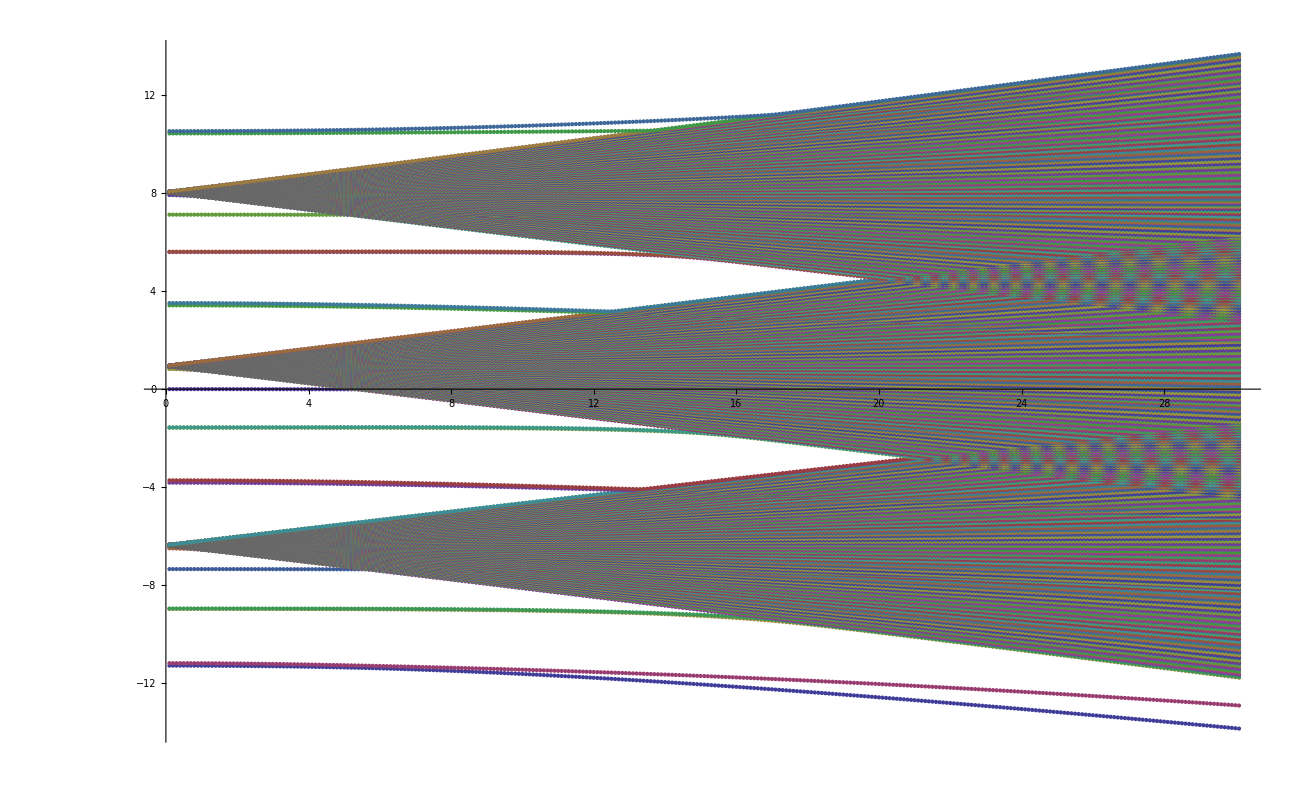

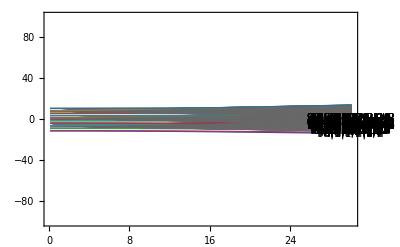

```mathematica
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=30.1;
ELabel=30;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=0.1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

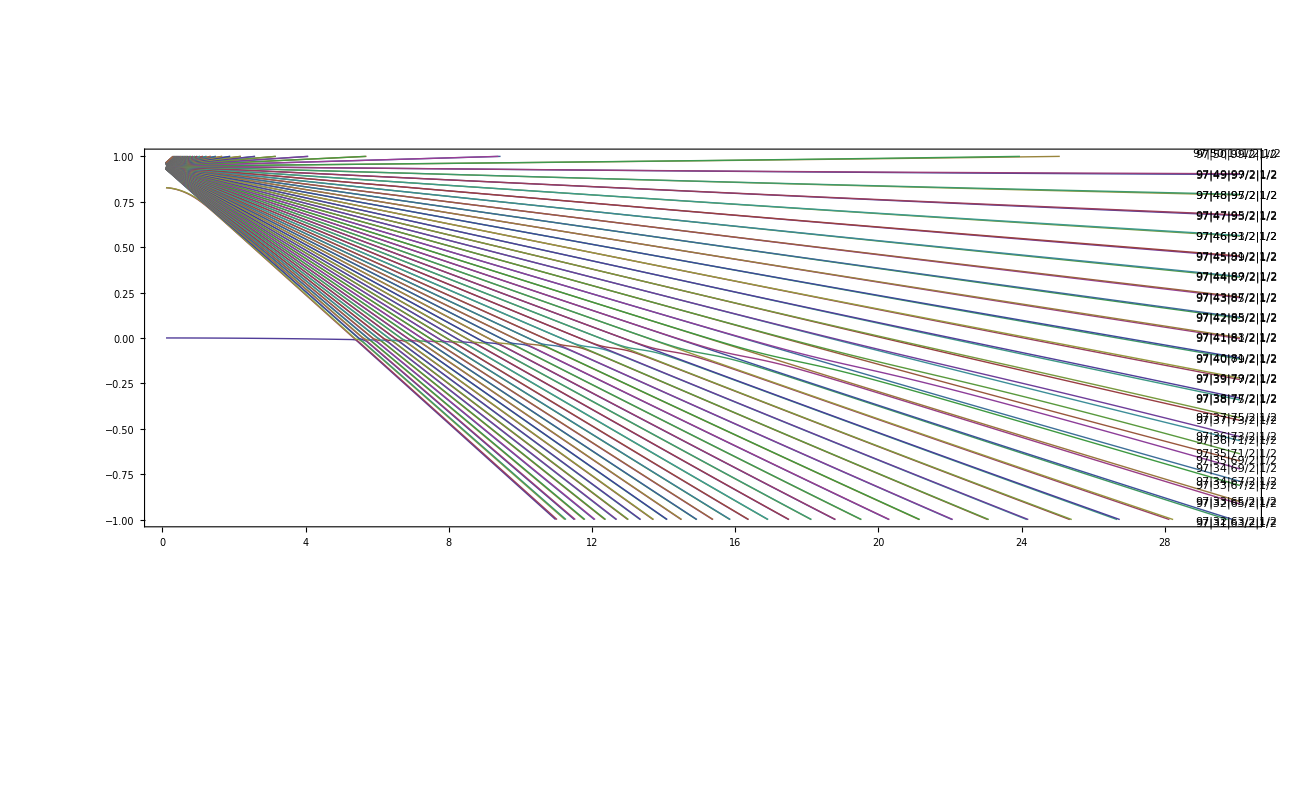

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
(*LabelList[[116]]

MPList[[116]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]

Export["60s_stark_Shift.dat",MPList[[116]]] *)
```

60|0|1/2|1/2

{{1,-8.9749×10^-6},{2,-0.0000358999},{3,-0.0000807756},{4,-0.000143603},{5,-0.000224385},{6,-0.000323122},{7,-0.000439819},{8,-0.000574477},{9,-0.000727101},{10,-0.000897695},{11,-0.00108626},{12,-0.00129281},{13,-0.00151735},{14,-0.00175988},{15,-0.0020204},{16,-0.00229894},{17,-0.00259549},{18,-0.00291006},{19,-0.00324267},{20,-0.00359332},{21,-0.00396203},{22,-0.0043488},{23,-0.00475365},{24,-0.0051766},{25,-0.00561765},{26,-0.00607681},{27,-0.00655412},{28,-0.00704957},{29,-0.00756319},{30,-0.008095},{31,-0.00864501},{32,-0.00921324},{33,-0.00979973},{34,-0.0104045},{35,-0.0110275},{36,-0.0116689},{37,-0.0123286},{38,-0.0130066},{39,-0.0137031},{40,-0.014418},{41,-0.0151513},{42,-0.0159031},{43,-0.0166735},{44,-0.0174624},{45,-0.0182699},{46,-0.019096},{47,-0.0199409},{48,-0.0208044},{49,-0.0216867},{50,-0.0225878},{51,-0.0235078},{52,-0.0244468},{53,-0.0254047},{54,-0.0263816},{55,-0.0273777},{56,-0.0283929},{57,-0.0294274},{58,-0.0304812},{59,-0.0315545},{60,-0.0326473},{61,-0.0337596},{62,-0.0348917},{63,-0.0360437},{64,-0.0372156},{65,-0.0384077},{66,-0.0396201},{67,-0.0408529},{68,-0.0421065},{69,-0.0433812},{70,-0.0446771},{71,-0.045995},{72,-0.0473352},{73,-0.0486988},{74,-0.0500873},{75,-0.0515034},{76,-0.0529536},{77,-0.0544608},{78,-0.0562774},{79,-0.0954785},{80,-0.155665},{81,-0.215968},{82,-0.276291},{83,-0.336621},{84,-0.396955},{85,-0.45729},{86,-0.517626},{87,-0.577963},{88,-0.6383},{89,-0.698637},{90,-0.758974},{91,-0.81931},{92,-0.879646},{93,-0.939982},{94,-1.00032},{95,-1.06065},{96,-1.12098},{97,-1.18132},{98,-1.24165},{99,-1.30198},{100,-1.36231},{101,-1.42264},{102,-1.48296},{103,-1.54329},{104,-1.60362},{105,-1.66394},{106,-1.72426},{107,-1.78458},{108,-1.8449},{109,-1.90522},{110,-1.96553},{111,-2.02584},{112,-2.08616},{113,-2.14646},{114,-2.20677},{115,-2.26707},{116,-2.32738},{117,-2.38768},{118,-2.44797},{119,-2.50827},{120,-2.56856},{121,-2.62885},{122,-2.68913},{123,-2.74941},{124,-2.80969},{125,-2.86996},{126,-2.93023},{127,-2.9905},{128,-3.05076},{129,-3.11102},{130,-3.17128},{131,-3.23153},{132,-3.29177},{133,-3.35201},{134,-3.41225},{135,-3.47248},{136,-3.5327},{137,-3.59292},{138,-3.65313},{139,-3.71334},{140,-3.77354},{141,-3.83373},{142,-3.89392},{143,-3.9541},{144,-4.01427},{145,-4.07443},{146,-4.13459},{147,-4.19473},{148,-4.25487},{149,-4.315},{150,-4.37512},{151,-4.43523},{152,-4.49533},{153,-4.55541},{154,-4.61549},{155,-4.67555},{156,-4.73561},{157,-4.79564},{158,-4.85567},{159,-4.91568},{160,-4.97568},{161,-5.03566},{162,-5.09562},{163,-5.15557},{164,-5.2155},{165,-5.27542},{166,-5.33531},{167,-5.39518},{168,-5.45504},{169,-5.51487},{170,-5.57468},{171,-5.63446},{172,-5.69422},{173,-5.75395},{174,-5.81366},{175,-5.87333},{176,-5.93298},{177,-5.99259},{178,-6.05217},{179,-6.11171},{180,-6.17122},{181,-6.23069},{182,-6.29012},{183,-6.3495},{184,-6.40884},{185,-6.46812},{186,-6.52736},{187,-6.58655},{188,-6.64567},{189,-6.70474},{190,-6.76375},{191,-6.82268},{192,-6.88155},{193,-6.94034},{194,-6.99906},{195,-7.05769},{196,-7.11623},{197,-7.17468},{198,-7.23303},{199,-7.29127},{200,-7.3494},{201,-7.40742},{202,-7.46531},{203,-7.52307},{204,-7.5807},{205,-7.63817},{206,-7.6955},{207,-7.75266},{208,-7.80965},{209,-7.86646},{210,-7.92309},{211,-7.97952},{212,-8.03576},{213,-8.09178},{214,-8.14758},{215,-8.20317},{216,-8.25852},{217,-8.31365},{218,-8.36854},{219,-8.42319},{220,-8.4776},{221,-8.53177},{222,-8.58571},{223,-8.63941},{224,-8.69288},{225,-8.74614},{226,-8.79918},{227,-8.85203},{228,-8.90469},{229,-8.95719},{230,-9.00955},{231,-9.0618},{232,-9.11394},{233,-9.16602},{234,-9.21806},{235,-9.27009},{236,-9.32212},{237,-9.37418},{238,-9.42631},{239,-9.4785},{240,-9.53079},{241,-9.58319},{242,-9.6357},{243,-9.68835},{244,-9.74113},{245,-9.79407},{246,-9.84715},{247,-9.90039},{248,-9.95378},{249,-10.0073},{250,-10.061},{251,-10.1149},{252,-10.1689},{253,-10.2231},{254,-10.2774},{255,-10.3318},{256,-10.3864},{257,-10.4412},{258,-10.496},{259,-10.551},{260,-10.6061},{261,-10.6614},{262,-10.7167},{263,-10.7721},{264,-10.8277},{265,-10.8833},{266,-10.9391},{267,-10.9949},{268,-11.0509},{269,-11.1069},{270,-11.163},{271,-11.2191},{272,-11.2754},{273,-11.3317},{274,-11.3881},{275,-11.4445},{276,-11.501},{277,-11.5576},{278,-11.6142},{279,-11.6709},{280,-11.7277},{281,-11.7845},{282,-11.8413},{283,-11.8982},{284,-11.9551},{285,-12.012},{286,-12.0691},{287,-12.1261},{288,-12.1832},{289,-12.2403},{290,-12.2974},{291,-12.3546},{292,-12.4118},{293,-12.4691},{294,-12.5263},{295,-12.5836},{296,-12.6409},{297,-12.6983},{298,-12.7556},{299,-12.813},{300,-12.8704},{301,-12.9278}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{«1»}

Stark_Shifts_around_60s.dat

Electric_fields_for_Stark_Shifts_around_60s.dat

60s_stark_Shift.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat